```mathematica
CloseKernels[]
```

{KernelObject[9,local,<defunct>],KernelObject[10,local,<defunct>],KernelObject[11,local,<defunct>],KernelObject[12,local,<defunct>]}

```mathematica
LaunchKernels[]
```

{KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

```mathematica
e=1;
m=2;
P=2^m;
Ep=1000;
Dynamic[{Ep,e,t}]
```

```mathematica
ParallelTable[(Label[New];
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
T=1999;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,n},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=10;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
c=Table[10*Price⟦1⟧,{i,1,n}];
NStock=Table[0,{i,1,n},{i,1,2}];
W=Table[10*Price⟦1⟧,{i,1,n}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
"initial set";
AgentStrategy=Table[RandomChoice[{1,-1}],{n},{S},{P}];
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}]];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,
Do[W⟦i⟧=10*Price⟦1⟧,{i,1,n}];
Do[c⟦i⟧=10*Price⟦1⟧,{i,1,n}];
Do[NStock⟦i,2⟧=0,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];];
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦i,s⟧=0,{s,1,S},{i,1,n1}];,
Do[PayoffFunction⟦i,s⟧=(AgentStrategy⟦i,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n1}];];
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Goto[sample],Goto[begin]];
Label[sample];
N[{W⟦1⟧,W⟦2⟧,Mean[W⟦1;;n⟧],Price⟦T⟧}]),{e,1,Ep}]//AbsoluteTiming
```

{19556.05467,{{4945.17,91542.3,8169.26,244.076},{4992.14,8195.36,4944.72,479.502},{5033.53,60687.,8431.57,765.675},{5052.64,17788.5,9454.36,197.907},{5007.26,12996.6,4941.35,480.895},{4968.86,45425.9,7654.34,735.028},{5100.4,5564.68,4937.88,520.896},{5007.26,-67797.4,5681.78,623.584},{5019.8,68425.,7162.07,712.142},{4997.31,-4947.69,8587.86,228.753},{4941.39,60018.9,5828.96,635.325},{4999.3,-17048.3,11472.8,137.01},{4986.77,35890.6,5799.72,632.738},{4941.99,17838.5,5131.13,434.925},{5000.5,121419.,6754.14,693.435},{5045.27,-80370.9,6854.1,697.216},{5047.07,-13161.5,4951.38,468.955},{5012.84,-44831.8,6329.09,667.763},{4990.75,-10227.8,5361.89,406.865},{5088.66,322684.,8626.83,773.038},{5059.2,92069.,6415.34,326.466},{5057.02,118473.,8565.24,770.849},{5013.23,144739.,7247.51,716.52},{4969.45,23736.6,5308.69,586.767},{4982.59,-2638.4,5151.11,432.536},{5085.47,-11975.8,10947.9,848.263},{5000.5,61776.1,7275.34,717.913},{4980.8,77856.3,6313.32,331.242},{4949.75,-23307.9,5064.81,556.717},{4976.42,3488.24,4969.81,469.154},{5027.16,-10465.6,4953.04,526.468},{4992.54,109745.,7870.84,743.585},{5039.1,5408.26,5063.45,446.865},{5009.25,-137472.,17909.3,-11.2501},{5012.64,-36333.5,5182.44,426.367},{4959.5,-13213.9,11809.7,127.259},{4973.03,82322.4,5731.47,627.166},{5098.61,-1646.35,5950.77,355.322},{5038.91,118191.,13555.2,916.722},{5057.02,17363.4,5619.46,619.006},{5045.67,110936.,17991.2,-12.8422},{5024.98,54305.4,9477.58,802.889},{5017.02,21233.1,5198.17,573.235},{5020.2,43037.2,6126.46,656.818},{4988.96,77262.5,5664.93,623.186},{4992.34,4875.52,4917.6,502.786},{5009.45,-36512.1,11253.,143.18},{4957.91,-58211.4,7336.63,720.699},{5043.88,136745.,5853.71,636.519},{4972.44,-129799.,7632.3,266.564},{4999.3,16454.2,7460.66,273.331},{4996.32,35215.,6496.06,322.087},{5028.76,13011.7,5452.69,605.474},{4952.93,15430.7,4977.03,464.577},{5004.68,29111.4,5123.07,437.114},{4992.14,25281.7,5096.92,439.303},{5050.25,-28279.3,6286.91,666.569},{4990.55,-27075.9,6739.46,308.157},{5045.27,16091.6,5255.94,582.588},{5064.38,7302.22,5130.67,431.939},{4994.53,-14118.9,6618.13,684.48},{5052.04,-27385.2,8096.94,753.137},{4964.68,30918.8,5076.52,557.911},{5035.72,141781.,14507.6,60.7906},{4981.39,38223.8,14276.2,65.9648},{4997.91,36727.7,14355.4,64.1737},{4980.2,-2170.14,6938.64,701.197},{5014.43,23798.5,5109.77,562.09},{5034.13,33813.2,6084.02,652.241},{5043.28,-17493.5,5978.68,646.469},{4991.14,4231.13,4919.19,500.398},{4998.51,-19130.5,5061.55,446.865},{5036.92,-188666.,7974.93,748.361},{5060.2,21400.5,4984.97,532.836},{4993.33,-42317.9,30690.5,1220.01},{5001.29,27073.6,5033.81,453.233},{4979.8,-18323.6,5729.22,628.36},{4994.53,15617.5,5817.89,637.912},{4979.4,23333.7,5399.77,402.287},{5019.4,-89227.9,7088.9,291.241},{4999.3,-811.515,5092.04,439.9},{4979.2,-103031.,6880.42,302.386},{4921.69,18430.7,6944.58,298.206},{5042.09,9869.81,6404.64,673.534},{4975.62,7035.15,6605.28,683.485},{5040.7,-28300.2,5040.02,454.825},{4995.32,47605.,10555.,163.478},{4968.06,-16582.9,6929.98,701.595},{5004.88,130529.,9913.08,817.019},{5012.64,23788.4,5123.55,435.323},{5010.45,-40163.6,5273.11,415.82},{4969.25,37580.2,5116.78,436.119},{5048.66,-150432.,8162.37,755.128},{5003.68,4107.75,5101.51,563.085},{5015.82,31090.6,9385.28,799.705},{4980.6,-10171.2,7509.84,728.063},{4967.66,69419.2,6049.11,349.351},{5007.46,-8407.03,5008.76,457.014},{5013.23,10711.4,4925.57,491.642},{5053.23,142684.,6944.36,701.993},{4980.2,-183482.,17587.,1004.88},{4987.16,22831.4,6253.51,336.217},{5035.52,92878.6,6578.7,316.316},{4974.63,570.592,5567.94,384.974},{5003.28,-20019.9,5143.88,566.468},{5001.89,23256.2,5041.22,451.641},{5017.41,12104.3,4936.24,478.109},{5009.45,-28791.6,8555.55,229.151},{5012.64,-50783.7,7285.71,281.888},{4990.15,-41113.9,9292.06,203.877},{5040.1,3809.84,6254.21,336.217},{4979.6,-2516.81,6091.31,346.167},{5022.79,2958.88,5782.34,632.34},{4993.73,-320.364,5428.85,397.312},{5001.09,-55372.8,6602.42,315.321},{4991.34,-1350.63,5257.39,418.407},{5027.96,-37897.9,5334.23,408.457},{4949.55,-22422.9,6271.51,665.176},{5058.41,10871.2,4923.43,516.319},{5055.62,24058.2,5019.34,455.82},{4993.93,-32933.9,7245.99,283.679},{4988.36,6346.19,4926.58,507.562},{5026.17,-81370.5,7218.83,715.127},{4979.4,2732.21,5220.83,421.79},{5044.88,-39991.3,5036.18,452.636},{5041.89,29704.1,6587.11,317.112},{5050.25,15063.7,6126.2,657.017},{4985.77,6434.35,5115.19,437.313},{5004.08,31912.7,5721.,627.564},{4983.98,22494.,7103.43,709.555},{4965.67,-47708.6,8487.38,767.665},{4992.74,6488.48,4976.49,465.97},{5023.58,6726.29,4933.56,500.796},{4940.4,-30399.7,5471.79,605.076},{5029.55,181002.,16992.,992.742},{5056.02,45999.8,5087.1,558.11},{4986.37,479379.,53892.7,-492.45},{4961.09,-41743.,6678.67,687.863},{5082.89,116416.,14600.1,941.199},{4999.9,-11973.4,6126.92,655.823},{5084.28,132210.,11523.6,135.816},{4946.17,-157703.,12102.5,880.303},{5004.28,4413.43,4933.56,477.711},{5037.31,19411.,5920.44,358.904},{4978.81,1251.6,4942.64,523.483},{5017.41,-101006.,6447.29,673.933},{5046.27,26379.5,6036.24,350.147},{5042.89,26811.7,7007.7,704.978},{4998.71,54800.3,5319.57,410.646},{5031.34,-66009.9,9511.28,803.685},{5014.03,-109052.,6310.69,667.166},{4991.14,62292.5,7082.54,290.843},{5069.16,10712.6,4951.29,524.876},{4996.12,103264.,8031.91,249.649},{4996.12,41671.6,10295.2,171.041},{5051.44,7986.41,4955.,524.876},{4965.87,13729.,5114.17,439.303},{4986.97,-38343.1,6120.3,344.575},{4981.79,17808.8,6095.29,653.634},{5019.8,-36727.,5143.17,566.866},{4986.97,15103.9,5968.7,645.076},{5024.18,-20127.8,5131.38,434.527},{5002.49,-46841.9,8989.36,214.026},{5061.39,-50294.3,15285.3,956.722},{5055.62,-126214.,7173.27,713.137},{4982.79,-103320.,14010.4,927.667},{5042.89,76867.5,9542.52,194.922},{5013.23,2986.34,4928.2,491.443},{5013.03,27731.9,5247.98,417.611},{5043.28,70521.9,6018.03,351.739},{4992.14,-20499.1,5840.5,636.718},{4970.85,-99421.1,7432.98,724.679},{5012.24,23501.6,5157.39,570.25},{4968.86,-23173.6,5463.58,395.322},{5069.16,38631.8,8246.13,758.511},{4944.18,27106.8,6475.96,676.719},{5003.48,-972.114,4960.09,523.284},{5047.46,10437.,4933.67,484.278},{5001.89,17369.2,5540.41,387.76},{4971.84,54046.9,7276.87,717.913},{4993.13,-3817.52,5247.13,416.417},{4959.3,42150.4,6322.73,331.242},{5014.43,172011.,9381.32,200.295},{4962.89,-62221.4,11571.5,866.174},{4959.7,1939.96,4985.13,535.622},{4979.6,54186.2,5696.56,375.023},{5030.75,137626.,8069.01,751.943},{5041.89,105901.,5870.81,362.088},{4998.91,-18773.1,4977.79,465.174},{5002.49,-2543.08,5929.82,357.71},{5048.06,114888.,8219.03,242.484},{4942.39,-66109.4,5360.16,594.728},{5064.58,272932.,12871.,99.796},{5052.64,100481.,6129.02,344.376},{4993.53,74339.5,6747.28,692.241},{5008.46,15147.1,7594.26,267.758},{5039.3,7767.5,5168.42,569.852},{4987.76,11136.7,4974.07,531.045},{4974.43,19285.6,5252.05,582.787},{5028.76,-63846.9,6772.81,306.963},{4962.49,82476.3,22667.4,-97.6193},{5042.29,77644.,10476.9,165.668},{5008.86,-27754.3,5104.64,439.104},{4995.92,64039.8,7723.41,738.013},{5017.02,5426.97,4925.19,491.443},{5014.63,-6527.21,4960.99,532.836},{5083.68,68597.9,11945.3,124.473},{4989.95,-228911.,26791.2,1163.29},{4969.85,164828.,13356.5,87.8556},{5073.73,-66402.,5995.08,351.54},{5044.68,20050.,8049.97,751.147},{4986.57,-16057.7,7235.86,715.923},{5049.25,67920.5,6928.31,299.201},{5016.02,4989.75,4933.02,494.428},{4986.37,-16748.8,5334.65,408.656},{4985.77,12371.3,5179.08,428.556},{5022.59,-157845.,9359.22,799.108},{5018.21,-36966.8,5760.87,369.849},{4954.92,-3240.8,5010.07,457.412},{4971.84,149781.,7494.92,728.461},{5057.61,-28613.6,6426.17,673.335},{5038.11,8788.8,4979.62,467.96},{5010.45,-15889.9,6071.93,651.644},{4975.82,10477.8,6391.37,328.257},{4999.9,-7226.72,5018.93,541.991},{5049.65,113586.,7069.56,707.764},{4981.99,10007.3,5635.92,381.193},{5065.57,143060.,7156.3,711.943},{4955.12,31562.6,7777.26,260.594},{5015.62,6924.1,4926.05,495.025},{5029.75,62980.9,5624.6,379.999},{5037.31,3440.88,8039.37,249.649},{4975.82,-67891.9,10068.2,821.795},{5012.64,-4193.85,5123.89,563.682},{5002.89,63569.8,6739.6,308.953},{5001.69,-182.054,4946.98,477.711},{5003.28,-22260.3,6284.64,334.028},{5017.21,7334.26,4925.44,490.448},{4980.6,43767.9,5200.85,427.362},{4949.95,-7061.34,6355.39,328.655},{4998.11,11722.4,4931.32,483.084},{5051.64,145719.,6540.16,319.699},{5041.49,85496.4,5728.56,629.156},{5010.65,18808.6,6291.45,665.375},{4981.19,12283.6,5515.67,390.944},{4980.6,5284.28,5132.78,567.265},{4986.57,18621.4,5038.95,449.452},{4985.97,12771.7,5430.72,399.103},{5018.41,-117398.,9097.04,210.245},{4955.12,-42330.6,6036.13,649.057},{4988.56,6915.75,7285.7,718.908},{5001.49,-4763.21,5000.28,540.797},{4967.86,-46536.5,11229.,856.024},{4993.33,11029.4,5206.9,424.775},{5040.5,114303.,6189.31,658.808},{4993.53,-631.811,5279.25,415.621},{4993.73,96708.5,10606.2,838.512},{4990.75,-24765.,5734.05,628.559},{4975.22,-37611.2,5543.23,387.362},{4941.19,-7785.33,5268.44,415.422},{5025.57,-36141.1,6012.91,649.057},{4979.,-123206.,6731.92,308.953},{5005.67,-50516.2,7371.73,721.893},{5015.22,27210.7,5169.23,428.954},{5035.12,-27509.2,5134.56,436.318},{4942.79,-58579.,7123.08,710.749},{4997.51,66158.7,5518.97,390.546},{4934.63,-67132.3,7620.07,732.242},{4955.32,-38409.2,5924.96,357.909},{5028.96,19137.,6465.3,323.48},{5019.4,60785.3,5499.12,607.464},{5072.34,15467.9,4915.79,495.423},{5015.22,130628.,7232.3,714.928},{4997.91,36487.5,6902.13,300.396},{5017.41,-86581.9,6415.49,672.937},{5034.33,-61521.7,9153.56,792.143},{5012.24,3641.87,4938.08,518.11},{5009.25,15199.4,4951.28,475.721},{4960.3,-193718.,14573.3,940.602},{5021.79,-26150.9,7177.71,287.261},{4991.14,55364.3,5648.57,620.001},{5036.52,26681.8,4929.26,494.826},{5022.99,-3446.57,5244.77,580.399},{5005.87,6651.07,5087.74,442.288},{5047.26,58419.1,6592.62,316.515},{5022.99,3055.4,5540.53,387.163},{5044.48,23721.3,5055.65,448.855},{5003.48,1130.8,5061.41,447.462},{5007.66,5265.58,4930.,485.472},{4980.2,-56283.8,5493.49,392.536},{4975.02,-26636.5,6038.68,650.251},{4990.35,-11031.9,5703.13,624.38},{5001.49,41529.7,5489.92,392.138},{5025.37,-18455.3,5239.34,418.208},{5004.28,121797.,8346.3,237.31},{5026.37,-13773.9,6799.78,695.226},{4980.6,-37788.9,5320.15,409.452},{5003.28,-17981.3,6205.48,660.201},{5001.69,-80464.2,9486.26,197.31},{5015.03,2248.82,4928.38,489.055},{5016.82,61653.5,5648.01,378.605},{4997.51,20307.,4957.41,474.328},{4999.9,35014.4,9006.36,786.969},{5004.88,-53894.2,6856.04,302.386},{5031.34,-65176.7,12894.1,900.801},{5006.47,-23827.7,5196.95,423.581},{5010.05,168149.,9122.34,790.75},{4998.11,25707.6,5131.02,434.328},{5007.46,58068.,8512.8,769.058},{5044.28,-15003.7,5077.08,554.13},{5029.75,80147.3,6456.1,676.122},{5035.72,13612.5,5338.98,407.462},{5034.53,7034.55,4931.33,495.224},{5060.,301604.,12093.9,880.104},{5011.84,34675.5,5411.59,399.501},{5023.18,34784.1,5465.46,394.924},{5032.74,21265.4,6291.64,665.375},{5005.47,33850.6,11848.7,873.139},{4957.31,-156835.,12084.,119.896},{5002.69,-78287.7,5460.8,396.317},{4975.02,-4996.84,5348.35,407.462},{4994.73,-41628.5,7787.09,739.605},{4967.26,-5917.05,4946.,478.308},{4998.31,189050.,9503.24,803.685},{5037.11,-14946.2,5455.86,396.317},{5030.15,19045.8,6794.94,694.828},{4974.63,-85733.6,12315.4,114.324},{5031.54,-3124.78,5722.91,373.431},{5007.66,25031.8,5196.5,426.765},{4940.,-82324.,8793.61,779.207},{5018.21,-5694.16,4989.95,534.627},{4980.6,42243.1,5449.95,606.27},{4974.83,-35934.5,6612.17,684.281},{5016.02,18495.8,6404.08,672.539},{4990.55,-37788.7,6290.34,334.028},{5005.47,6851.27,5096.48,441.094},{4934.83,-77559.9,28481.4,-188.367},{5002.49,17513.3,4993.07,458.606},{4980.6,9125.92,4964.71,469.353},{5066.57,76345.9,6860.31,697.415},{5054.23,58057.9,5812.76,633.733},{4967.66,-39098.,5582.13,616.817},{4957.31,-130365.,11804.4,128.254},{5003.48,-106531.,7362.29,278.107},{5013.43,-8208.82,7195.66,285.669},{4975.22,-73786.5,5043.52,549.354},{5024.18,-4378.13,5870.69,362.088},{4948.95,-26401.9,5429.24,398.904},{4991.54,-1291.32,5094.69,441.492},{4978.61,-92719.1,9846.38,185.369},{5012.04,70326.3,7532.24,270.743},{5046.67,-66883.2,9940.87,818.213},{5071.34,-138928.,9829.5,185.568},{4971.04,-12607.3,4963.75,526.667},{5041.29,-66263.3,7266.91,282.286},{4943.98,44650.5,7714.96,737.018},{5016.42,152182.,7262.83,716.918},{5014.83,78233.6,9414.56,199.101},{4954.53,5960.11,4956.63,523.483},{4947.16,-26617.6,5102.82,439.502},{5046.07,-9575.01,4961.15,527.662},{5038.91,-40376.,6106.9,344.973},{4978.81,1820.36,4931.87,481.691},{4995.72,66298.2,6470.64,676.321},{4991.14,3288.24,4923.04,492.438},{4944.58,8713.78,4915.75,484.079},{4967.86,4807.46,4917.89,499.005},{5006.67,3885.06,4924.17,515.921},{5003.68,32763.8,5155.8,571.046},{5026.97,4413.23,5380.76,596.917},{5054.63,-2663.88,6069.65,652.639},{4955.72,15967.,5057.35,446.666},{4973.23,-16461.1,5645.52,620.599},{5044.08,-50340.1,5644.67,378.008},{5016.82,55188.2,5672.08,622.987},{5031.34,5446.87,4931.29,508.756},{4984.38,48497.6,5952.03,355.72},{5041.69,49872.9,6269.97,335.421},{5011.04,12791.6,4964.5,522.687},{5033.73,10954.2,4939.1,479.104},{5000.1,34066.1,5336.48,409.452},{5025.97,-35628.9,5844.25,364.675},{4987.76,6501.81,4946.36,516.518},{5042.09,55675.6,13247.1,91.0397},{4950.94,-24421.,5074.08,555.523},{5021.19,-39284.8,5972.28,646.867},{5010.65,15453.6,5455.59,606.469},{5036.32,61620.3,5683.59,623.982},{5045.47,90422.8,5768.16,368.854},{5011.04,-1211.72,4968.4,461.592},{5002.29,-98942.5,7747.93,261.788},{4987.36,-37061.9,6309.24,667.365},{5023.98,124804.,7504.22,727.665},{5059.2,27325.5,9391.71,199.897},{4987.36,10528.7,5045.6,447.462},{4986.17,-86548.7,6133.28,344.575},{5020.2,44673.2,7700.97,736.023},{4975.02,-41564.9,21614.2,-79.5097},{5043.48,-30134.9,8023.56,749.356},{5000.1,52148.1,5235.22,420.397},{5002.69,-6548.3,5328.1,590.946},{4973.23,33784.7,6125.72,656.221},{5042.69,5548.36,4929.2,509.95},{4999.3,11900.7,5617.35,618.409},{4960.1,-7491.4,5416.05,599.305},{4965.07,10173.7,5216.26,578.807},{5063.78,17116.3,5014.97,457.412},{5031.74,30515.6,5227.48,421.79},{4978.61,-43722.3,5243.47,580.797},{5000.5,8249.69,4947.96,521.891},{5019.6,12983.7,4993.9,537.612},{5025.37,-5000.62,5229.32,580.399},{4968.46,100833.,7886.1,744.58},{4996.32,122937.,12952.8,98.005},{5009.25,32826.1,8931.32,783.984},{4983.78,-1428.64,14585.9,941.},{5017.61,34432.1,5765.77,630.748},{5043.48,16298.1,5428.28,601.693},{5029.95,-14756.,6901.42,700.799},{5026.77,-3000.6,14516.4,60.1936},{5025.77,12767.4,5388.6,597.116},{5045.67,137208.,8397.3,764.083},{5039.5,9580.85,4922.19,491.443},{5003.88,8461.04,4922.24,492.836},{5045.67,93935.7,6820.73,695.624},{5054.83,-62732.3,6286.56,665.574},{4999.3,73573.5,7031.99,706.371},{4971.64,30747.7,6318.96,667.166},{4942.19,13321.2,4923.95,517.911},{4978.21,-47606.7,8855.65,780.999},{4994.93,-5327.79,5399.14,599.106},{4966.47,-86873.7,5851.8,363.879},{5021.99,6467.58,4939.79,517.115},{5025.57,-110194.,19511.,1041.9},{4986.77,-83802.8,9334.14,202.086},{5044.28,2455.79,5031.,546.767},{4982.59,-61910.4,5632.69,379.202},{5074.33,4254.22,4934.89,517.115},{4990.55,-31548.2,6162.34,657.415},{4979.2,8341.63,4934.44,486.467},{4965.27,2615.99,4955.75,533.234},{5033.93,-19313.6,9840.47,185.568},{4958.11,-86856.8,7918.95,745.575},{4980.,-9015.,5432.62,398.705},{5011.84,10223.6,5151.01,427.959},{5023.98,15238.6,4997.11,453.83},{4997.71,61038.6,5790.57,632.34},{5032.54,-29661.6,9359.77,201.29},{5038.71,4592.13,4917.81,507.164},{5028.36,-59740.4,7284.15,281.49},{5051.24,-3399.61,5064.15,446.467},{5008.26,32336.,5349.83,407.462},{4998.91,-20146.1,5409.72,597.514},{4987.76,-63760.4,10863.2,845.875},{5006.47,23058.,9112.37,209.449},{5005.67,17562.6,8087.84,247.659},{4973.03,8210.69,4936.58,514.528},{5020.6,95172.4,10687.1,159.1},{5002.89,12065.9,6357.86,670.151},{4998.11,71614.1,7118.52,710.152},{5032.74,-75426.4,6200.83,660.201},{5005.87,43572.7,5774.1,630.549},{5003.68,-42903.4,5647.01,378.207},{5001.69,6339.82,7161.79,287.659},{5011.84,-22415.,9523.89,804.481},{4995.12,17297.8,5368.24,404.675},{5025.77,-57991.5,5118.2,438.109},{4966.47,31233.3,5206.67,576.618},{4991.54,20771.4,5282.66,414.427},{5000.9,18564.8,4982.5,536.219},{5005.27,-60869.6,8746.83,222.385},{4949.75,-3515.83,4919.68,502.786},{4970.65,15696.7,5049.05,449.452},{4986.57,-3113.23,5447.16,603.484},{5038.51,-50319.,5444.07,396.715},{4961.29,16076.7,4980.47,536.219},{5002.89,108647.,15455.7,39.8948},{4969.65,53582.,7513.25,727.864},{5015.22,25339.1,5524.1,610.25},{5023.98,-104133.,7220.95,284.276},{5030.15,-22170.2,5247.27,417.412},{5019.6,67836.3,5611.53,618.011},{4969.45,4083.67,5403.28,598.509},{5019.6,-86420.7,6303.16,333.232},{4968.26,106504.,15910.,29.9444},{4987.56,-64818.5,5810.41,365.869},{5026.37,-77387.8,5732.81,628.161},{5019.8,5628.96,5025.33,454.427},{4957.51,103704.,11406.2,861.398},{4996.72,-27741.6,5935.07,356.914},{4968.46,-6372.78,5156.76,429.153},{5000.9,31667.5,5264.89,582.787},{5029.35,14510.3,4932.72,495.224},{5023.18,5470.55,4939.42,487.861},{4977.01,8284.52,4903.27,486.866},{5018.61,23826.,5393.77,403.68},{4978.01,-98290.9,5740.66,370.446},{5000.7,9088.51,5490.08,391.541},{5080.7,51935.6,11696.3,130.642},{5024.18,40397.8,7690.88,263.977},{5012.64,13234.4,5136.1,566.07},{5018.81,67087.,6939.7,701.794},{4965.07,-11195.7,5017.9,454.427},{4993.33,6699.42,4988.11,461.194},{5059.2,76067.8,6066.18,651.644},{4979.,-193639.,11219.7,856.223},{4982.39,-21796.8,5677.83,377.013},{4974.23,147046.,18639.9,1025.58},{4965.07,-12448.3,4948.69,480.497},{5010.85,-62845.3,7923.31,745.973},{5030.15,148559.,6835.28,303.381},{4963.08,20857.,4975.59,528.856},{5002.09,106289.,7244.16,716.122},{5045.87,-68145.1,6360.93,670.35},{5001.09,-111143.,13049.4,95.8159},{4988.76,-36796.,6315.79,666.967},{4938.61,-70966.2,6426.02,674.729},{4964.28,-136488.,6440.84,675.326},{4975.62,14726.8,6381.84,670.947},{4972.24,81818.4,18459.1,1022.},{4969.65,-5953.67,8141.41,245.668},{4961.09,-102797.,7949.61,747.167},{4996.52,56278.7,10059.1,820.999},{5010.65,18497.2,5728.17,372.436},{4903.38,2484.05,4932.71,515.921},{5033.93,26627.4,10685.,841.298},{5065.77,182298.,9851.7,185.17},{4962.49,-72033.7,7465.53,726.868},{4959.5,4481.29,4941.16,532.239},{5016.22,21401.3,4920.98,500.995},{4971.24,-71248.8,7365.85,721.694},{4996.92,-158050.,6963.76,701.993},{4971.24,38247.3,5812.9,634.33},{5011.24,-15431.,5171.99,429.153},{4989.95,36204.3,5039.96,550.946},{5051.24,-174088.,17460.3,-2.29477},{5028.16,115134.,18453.4,-21.5985},{5045.08,-79574.9,6977.31,703.386},{5033.33,30165.4,5656.46,622.39},{4975.42,49458.6,5511.98,610.648},{5058.41,75450.7,14475.5,61.7856},{4971.84,-144743.,16219.1,23.3772},{4997.51,35962.9,5015.91,456.019},{5025.57,-52668.1,6261.85,335.62},{4940.6,17983.5,4931.09,480.696},{4955.92,29376.3,5161.72,429.551},{4984.58,31622.9,5987.37,352.535},{4988.16,18834.1,6855.38,697.614},{5032.54,-70709.1,6387.02,328.456},{4990.95,-2319.99,6181.47,340.396},{4951.94,88143.6,6209.62,339.202},{5081.29,-24112.9,5089.68,557.314},{5008.26,-35774.7,6647.09,314.326},{4966.27,4892.83,4950.57,523.284},{5027.96,-4475.24,8857.46,218.205},{5026.57,45628.1,4998.8,540.},{4992.14,-96607.7,6364.03,328.854},{4987.76,54348.4,5073.41,444.676},{4949.55,37695.6,6609.65,314.923},{5004.08,41341.4,5055.2,551.145},{5039.3,-146475.,7206.81,716.122},{4984.97,40391.6,5391.07,598.111},{5008.26,-41957.5,5646.58,379.6},{4997.51,23619.4,14710.9,56.2134},{5080.7,-68431.1,9008.32,213.429},{4930.65,21816.,17807.8,-9.45904},{4995.52,51004.4,11019.9,850.85},{5040.1,319454.,18544.9,-23.5886},{4937.41,-152335.,15798.2,31.9345},{5035.92,-45123.5,7784.78,740.401},{4991.14,-70923.,7601.81,732.242},{4977.01,-23299.6,6569.43,317.311},{4978.21,11351.,4970.91,530.448},{5028.16,7331.07,5095.2,442.686},{4997.91,60797.4,7927.16,745.774},{5035.52,75660.9,5264.62,584.578},{4975.42,8341.83,4981.23,466.965},{5027.16,59821.1,7176.14,713.137},{5024.38,61760.2,9296.02,203.28},{4998.91,-68388.9,7455.29,725.475},{4919.1,-177810.,16106.4,25.3673},{5036.52,69412.6,5404.87,401.093},{5036.52,8254.87,4979.1,536.418},{5050.25,91596.2,5738.59,370.645},{5022.79,32752.3,13637.6,81.0893},{5011.84,21678.1,5316.87,590.15},{5067.96,14198.6,5336.85,407.462},{4913.33,-40894.2,6035.35,649.057},{5042.29,102551.,9216.7,205.668},{5005.07,-22355.3,5406.86,399.302},{4996.32,-57347.9,5706.93,372.834},{5050.25,56352.6,5789.85,367.461},{5000.1,-11605.3,4991.62,463.98},{4976.82,2276.28,4968.42,533.831},{5014.63,76882.8,16347.7,979.608},{5009.45,-39315.1,9448.97,198.703},{4989.75,-3667.67,5384.33,596.121},{4984.38,-9740.78,5651.38,620.599},{5009.25,11584.9,10856.1,845.477},{5090.45,-10751.1,5532.21,611.046},{4985.57,79157.,5851.91,636.32},{4959.3,5111.74,4927.36,504.378},{4955.92,12959.2,5186.61,571.643},{4972.84,12412.3,4929.14,479.9},{4982.79,13115.6,13531.2,83.8754},{4965.67,10730.5,6079.21,347.361},{5029.35,-11282.1,6636.95,313.331},{5025.37,-7386.72,4992.06,463.383},{4935.82,37394.5,5145.06,430.148},{5032.74,-27245.9,6394.02,672.539},{5023.98,-19163.6,4923.17,485.074},{5048.66,8667.41,4935.6,494.03},{4998.11,2749.52,4967.23,472.736},{5002.69,6221.01,5035.72,547.364},{4980.6,-137771.,10037.3,820.999},{4992.74,8994.38,5271.26,583.981},{4988.16,2982.76,5076.36,555.722},{5056.62,11386.4,6985.84,703.784},{5019.4,33096.8,5884.12,639.106},{5008.46,-5825.91,5195.39,425.173},{4998.51,75874.6,7513.42,728.262},{5032.74,43963.6,6397.55,327.859},{5043.28,2426.14,4996.17,540.},{4975.62,-37719.,8658.74,225.768},{5021.,16411.8,4976.65,465.373},{4995.12,-56737.6,6522.71,319.699},{5017.21,-55302.7,5470.42,394.725},{4983.18,-43882.7,7167.78,712.739},{5042.69,-74828.4,8630.77,773.237},{4931.04,10126.5,5825.21,363.879},{5004.88,127108.,9854.86,815.029},{4965.67,-2667.06,4971.66,531.642},{5028.16,-4762.61,5600.37,617.016},{5005.27,7504.81,4921.35,502.587},{4970.65,-172986.,14723.7,54.8204},{5017.61,-16677.8,4996.2,538.806},{4995.32,46370.4,16714.3,986.971},{4958.11,4760.1,4928.55,502.985},{4992.14,112092.,10341.5,170.046},{5054.63,16108.1,4979.33,533.632},{5009.25,48386.7,6388.5,328.257},{4991.54,30456.3,6753.09,307.958},{4986.17,18399.3,5123.89,431.74},{4938.21,-34973.9,5185.8,573.832},{5051.84,-123257.,10069.6,177.608},{4952.54,7440.13,5970.27,646.469},{5034.73,82535.4,5634.18,620.599},{5026.77,12521.6,5471.4,605.872},{4981.99,-4861.52,4917.93,486.467},{4996.92,132861.,13585.9,82.4824},{5009.85,-97367.7,15874.3,969.459},{5026.57,-29556.9,5142.52,567.265},{5031.54,81903.1,5503.18,391.541},{5048.46,9522.74,4968.35,471.144},{5008.06,-214136.,15530.7,37.9047},{5079.3,20698.2,5067.32,554.329},{5035.92,32550.7,5303.11,412.636},{4992.54,47333.8,7445.23,274.923},{5038.51,95505.3,5980.22,645.872},{4966.47,3352.72,4929.02,496.418},{5050.45,32948.7,11271.9,142.782},{4965.67,-20450.4,6086.93,654.032},{5013.23,82035.3,5864.45,360.297},{4983.98,18647.,5152.94,572.041},{5036.12,9944.64,4957.45,528.458},{5007.86,-19528.6,5961.39,644.479},{5017.21,56558.9,5160.78,569.653},{5028.56,234569.,14041.2,928.662},{5041.1,67693.6,8185.01,244.275},{5014.83,25137.1,5123.31,431.74},{4933.23,-50420.7,6173.99,659.206},{5025.57,7172.46,5023.99,547.563},{5019.8,-66419.9,9981.88,180.991},{4988.76,34504.1,5598.61,617.016},{4992.14,-74776.,5848.72,364.675},{5011.44,-56121.3,8938.87,215.618},{4996.12,4873.13,5398.01,402.486},{4951.94,3284.46,5186.88,572.837},{5042.29,84581.8,5302.61,413.034},{5042.09,44894.3,8999.32,213.628},{5000.1,-101594.,7859.84,743.983},{4971.44,15555.3,4936.61,514.727},{5024.18,-13861.2,6416.93,672.738},{5036.12,-30634.2,5766.9,631.942},{5011.84,-50915.2,10794.6,155.518},{4959.7,11580.1,5390.92,598.907},{4964.28,59922.4,10386.9,168.056},{5033.53,116057.,5896.9,359.7},{4983.98,11565.8,4931.4,515.921},{5027.36,-3095.72,8163.65,243.877},{5005.27,-289545.,12124.6,880.9},{4959.1,-6421.73,7981.63,252.037},{4945.37,-18948.1,7326.56,279.5},{4997.11,-2255.71,4969.16,470.149},{4990.75,1886.23,6587.75,317.311},{4958.71,70344.2,6552.57,681.495},{4980.99,-156206.,15298.9,43.2779},{5000.5,25238.,5921.46,358.108},{4994.93,71495.8,9279.79,796.123},{4947.16,4913.33,4936.72,472.139},{4973.03,7186.99,6018.53,350.943},{4998.91,16820.5,6001.36,647.266},{5023.98,-9168.63,12062.5,120.692},{5003.08,25689.1,8201.4,243.678},{4982.39,12099.3,11002.3,150.344},{5079.5,92875.8,6883.24,698.609},{5013.63,-1400.97,4950.,472.935},{4944.38,2666.34,4955.03,530.846},{5042.89,21933.6,7525.42,729.257},{4964.68,-57707.5,6311.98,332.436},{5092.04,381068.,16745.6,987.966},{5030.75,1113.68,8390.33,235.718},{5028.76,-15925.9,13211.2,91.8357},{5021.79,-2465.47,4957.89,476.517},{5028.96,-44406.7,7155.36,287.659},{4977.01,-106910.,9687.39,809.457},{5046.87,-63606.9,6649.93,686.271},{4986.97,93117.2,6977.55,296.216},{5031.34,39583.6,8858.33,218.603},{5043.68,-2245.76,5064.64,553.135},{5030.95,40385.2,5201.94,576.419},{5008.26,-69539.7,7846.91,257.41},{4974.63,-21681.,14817.,946.175},{4974.83,3150.92,5341.31,407.064},{5019.8,-10345.4,4990.34,537.015},{4958.51,-42744.2,6376.18,328.058},{5027.96,4506.36,5008.4,542.588},{5045.47,6415.44,4936.93,515.921},{5026.97,76153.8,11045.4,148.553},{4988.96,-13736.3,5091.22,558.508},{4980.,20344.,5358.69,403.282},{5028.76,-14239.1,5129.74,434.328},{4963.28,-44912.8,6511.62,321.291},{5025.57,81129.,5463.5,603.683},{4921.89,12708.9,6328.12,331.839},{4991.74,138.746,5385.77,403.282},{5036.32,55789.4,5317.53,588.757},{5017.02,-44346.2,8099.56,247.062},{5025.37,75907.,5901.16,359.7},{4998.71,6182.6,8423.91,233.728},{5014.43,-51630.5,6111.39,655.226},{5031.54,-30200.1,6035.09,650.45},{5026.37,-17679.2,5495.03,606.867},{5072.74,27098.5,5221.24,421.392},{4967.46,-182471.,11293.6,141.588},{5056.82,40506.,5272.37,584.379},{5024.98,23633.,5160.53,428.755},{4984.38,31274.7,5350.33,408.059},{5003.68,140691.,5867.2,638.31},{4985.97,-50058.1,6647.72,687.266},{4973.83,-72109.1,6353.27,330.645},{5034.13,3413.61,4937.05,524.876},{5011.44,147831.,5822.18,364.078},{4982.98,-1574.31,5071.89,553.931},{4958.9,-138255.,8742.52,777.814},{4970.65,90015.1,5582.21,384.775},{5030.95,19550.5,5022.96,543.782},{4991.54,-11576.4,7344.17,720.5},{4942.39,1434.88,4951.,528.06},{5006.67,-422497.,17236.5,2.2824},{5054.63,8868.61,4913.92,503.184},{5021.,17478.7,5603.52,618.21},{4991.54,36063.8,5013.89,543.384},{5018.41,11592.4,5093.92,559.901},{4973.03,5963.3,4943.3,483.681},{5024.18,411129.,18366.,1020.21},{5013.63,-4596.04,6674.18,687.863},{5059.6,193061.,12835.,100.393},{5006.27,37145.,5794.79,367.063},{4981.59,-69736.1,6904.74,299.6},{5011.44,23722.3,5765.55,630.549},{5018.61,-5403.61,6660.81,312.535},{5040.3,34959.9,5489.23,607.265},{5022.99,2976.59,4924.51,501.791},{4977.81,-823.853,4999.07,460.597},{5044.28,84283.7,7533.82,729.058},{4997.11,13874.4,4918.96,494.826},{5007.26,-41678.1,8315.72,761.496},{5037.31,1924.24,5121.33,437.711},{4989.15,115478.,6611.07,315.321},{4966.67,53810.9,5748.31,628.559},{4984.78,14161.6,5040.26,450.447},{4973.63,-3187.86,5324.66,590.349},{5052.84,44400.4,7546.43,269.947},{4969.05,-12916.5,4935.32,526.866},{5013.23,61089.,10299.5,829.556},{4963.48,-447687.,14441.5,62.3826},{5002.29,-6296.16,5239.94,420.994},{4985.57,7803.72,5010.27,542.19},{5091.64,22334.6,4939.2,520.896},{5009.25,5708.76,5273.7,416.218},{5022.39,246944.,10727.4,158.503},{4938.01,54199.9,6215.13,337.411},{4997.91,-90854.4,8340.96,762.69},{5028.36,271087.,10931.4,152.135},{5015.03,18995.9,5110.46,439.701},{5040.5,36852.6,5645.67,378.406},{4986.77,-71862.5,6741.11,308.356},{4984.97,-7170.,4941.24,520.299},{5015.03,-47547.2,5040.5,545.573},{5004.68,24495.3,9668.62,190.941},{5041.29,28842.,5084.52,557.712},{4934.83,71646.7,8121.28,246.067},{4984.18,6046.48,5022.39,546.17},{5062.99,-995.597,5367.77,596.718},{5040.1,114044.,12087.,120.294},{5068.56,190580.,6359.97,329.451},{4985.17,15244.8,4966.46,468.358},{4961.49,-184513.,11815.9,871.945},{5056.22,-43382.6,5792.17,632.34},{5020.,8786.02,5151.37,430.546},{4998.51,112244.,5995.29,352.734},{5046.87,-25816.4,5160.06,432.337},{5058.41,14977.9,5446.97,601.693},{5001.89,115894.,9234.54,205.071},{5040.9,-14971.7,5266.58,583.583},{5011.64,-528.128,5392.32,402.088},{5023.58,37474.3,5382.52,596.718},{5019.01,5161.89,4916.34,507.164},{5027.76,-28931.7,6358.16,329.65},{5031.54,-119064.,7468.88,726.47},{5001.09,-3412.34,5148.08,568.658},{5045.27,42516.8,5088.22,559.503},{4992.94,39818.2,15668.2,965.876},{4972.84,37464.4,5457.81,603.484},{5009.85,-14959.2,5038.86,450.646},{5009.65,71190.4,5955.07,644.479},{4965.87,-19921.4,5778.56,368.655},{4995.32,6753.75,4911.19,507.164},{4958.71,2097.58,5602.61,383.183},{4999.3,-81889.7,10812.7,155.916},{5024.78,46220.5,5702.99,625.972},{4979.,-53973.,7486.27,726.868},{5030.75,2453.,4942.33,513.931},{4999.3,-76818.8,6751.15,693.037},{5083.88,7063.41,5898.46,639.902},{4985.77,1905.53,4931.29,484.676},{5014.83,1532.2,5029.77,551.941},{5010.65,-118737.,16206.1,22.7802},{5046.87,62972.6,5941.86,643.683},{5036.92,30227.9,7800.84,741.396},{4994.93,16042.2,4971.9,468.756},{5017.81,122734.,6191.57,660.4},{4981.99,-33661.5,8593.69,772.64},{5017.41,-10378.4,4928.24,486.467},{5013.23,-58592.7,15914.9,970.454},{4983.18,10787.6,5320.18,409.054},{5005.47,31291.6,5503.65,608.459},{5035.32,12750.6,6135.07,342.983},{4977.61,17158.1,4987.36,539.204},{4954.92,-62986.4,7828.12,258.007},{4988.96,2261.76,5378.24,402.685},{5067.56,7062.41,4914.54,521.891},{5020.,-38300.3,5713.19,373.829},{4938.21,-129567.,35341.3,1282.3},{4982.19,16309.7,5394.44,401.491},{5016.22,8917.76,5256.64,416.019},{5017.41,46462.5,5699.42,374.426},{5010.65,7388.79,7699.47,263.579},{4991.74,78229.7,7095.69,709.157},{4984.18,55164.1,7514.07,729.257},{5028.76,66539.4,5338.76,591.941},{5041.1,54519.5,5067.61,555.125},{4933.23,-27735.2,7991.33,749.356},{4983.98,26006.9,7868.84,256.017},{5010.65,-158217.,8930.76,215.817},{5033.53,24333.3,6988.69,295.619},{4975.62,9801.35,4976.69,464.577},{4985.37,115187.,7724.45,261.987},{5003.28,-38959.3,5555.24,613.434},{5034.13,-7816.58,5836.17,363.481},{5082.89,98903.7,5193.48,574.628},{5001.89,5477.72,4947.12,479.502},{5048.06,69617.,6179.13,341.391},{5020.2,125081.,28837.,1193.54},{5091.24,21313.1,5018.96,458.606},{4949.55,-81447.3,7877.57,744.381},{4979.4,-1916.4,4958.67,529.254},{5008.06,50492.4,4987.51,533.632},{5030.15,3926.65,4912.68,498.209},{5082.49,16482.6,9174.86,207.459},{5009.25,10194.8,4942.27,479.303},{4988.36,13560.6,4995.09,540.797},{4986.77,98442.1,17515.8,-3.28981},{4967.46,-51495.3,7525.59,729.456},{4998.91,8082.53,5179.95,572.439},{4953.93,-28292.7,21738.9,-82.0968},{5004.28,4254.42,4958.99,473.93},{5021.19,8710.39,4944.12,519.702},{4970.05,7390.97,5142.26,566.07},{4976.82,7929.29,4987.62,464.378},{4993.53,-712.011,6245.98,664.579},{4976.42,30317.4,8980.99,785.775},{5059.2,-11579.,4988.54,540.2},{5019.2,16424.3,6316.3,667.763},{5044.28,-67723.6,5871.6,639.106},{5021.39,9572.1,5963.41,643.882},{5062.99,-58380.2,6463.27,323.48},{4988.96,4340.79,4975.17,533.831},{5023.98,10922.4,5365.65,405.869},{4959.1,-5938.94,5576.21,385.173},{5011.64,4798.31,5044.89,451.243},{5042.69,56480.7,18180.5,1016.42},{5022.39,54334.4,5850.7,363.481},{5029.35,-51009.2,6572.88,318.107},{4964.88,-143490.,10538.1,163.08},{5032.94,1083.43,4920.69,508.358},{5014.43,22374.4,5203.66,422.785},{4968.66,-75311.7,8684.,774.829},{4971.04,19047.6,6880.28,301.59},{5037.31,3254.8,4910.85,489.453},{4980.6,337.753,5182.81,427.959},{4939.6,-79121.9,11312.,141.588},{5045.67,-345149.,15492.8,960.901},{5038.31,-4808.18,5031.47,450.646},{5013.43,39669.8,9685.87,809.656},{4994.73,4327.26,4935.13,482.885},{4991.94,5583.99,5281.39,585.175},{5045.67,-1356.2,5075.37,442.487},{4993.33,94699.5,7113.08,289.848},{4992.14,-16324.5,5238.12,417.611},{4990.95,5001.29,4939.23,485.472},{5017.41,-20932.6,6700.03,310.147},{4959.9,7851.28,4949.55,525.871},{5010.25,-38910.1,6447.22,324.276},{4960.9,87073.6,12344.2,886.671},{4948.76,85703.6,6510.17,679.107},{4978.41,-8522.46,5372.1,596.32},{5009.25,97.3523,4923.23,484.278},{4987.36,5886.68,4911.63,495.423},{4981.19,-47185.2,5504.3,392.138},{5019.2,-79784.6,7341.76,721.097},{5016.42,82756.5,5204.98,575.623},{4949.75,18936.6,5094.22,559.503},{5070.15,-170961.,8418.,765.874},{4967.46,18193.7,6204.34,339.401},{5039.7,-13452.3,7849.26,256.813},{4988.76,81461.5,5613.29,381.591},{4997.51,28137.3,9722.94,189.349},{4986.97,-37295.3,5547.13,613.036},{4978.21,86653.4,6292.71,665.375},{5035.52,-107534.,11779.9,128.453},{5020.4,-184021.,10419.7,167.459},{4994.93,21240.3,5409.84,402.088},{4986.17,22631.8,5067.76,554.329},{5081.69,-26268.1,7525.81,270.942},{5014.83,275810.,20016.1,-51.0516},{4958.11,23338.4,5401.16,597.315},{5021.,56022.,6299.67,667.365},{5048.86,11109.,5554.61,612.837},{4988.76,3621.97,4935.22,490.249},{5034.93,157049.,6344.81,670.35},{4976.22,15185.3,4992.32,540.2},{5065.57,176538.,12086.4,879.905},{4994.93,-12647.5,5048.59,551.543},{5079.11,115094.,8952.14,215.618},{5005.07,32359.2,13695.,79.6963},{5028.76,5965.09,5270.98,583.583},{5028.96,6401.11,5171.53,569.653},{4989.95,-32298.1,6219.17,661.196},{5006.87,2413.6,5736.25,371.441},{4951.34,-70770.2,5807.57,366.466},{5066.37,-2862.09,4933.43,481.094},{5077.31,80954.9,5577.85,384.775},{5034.13,15550.7,5019.38,543.185},{5000.1,36476.5,5555.4,386.168},{4940.2,-13034.6,5752.1,629.355},{4947.96,5475.93,5062.65,447.064},{4978.41,-79903.2,12086.5,879.507},{5110.35,206749.,11258.3,142.583},{5012.04,20890.2,5448.61,395.72},{5050.05,23638.9,4975.33,464.179},{5028.96,-3967.37,4958.9,478.507},{5039.3,-66953.,12314.3,113.926},{5005.27,-26285.3,5518.94,390.347},{5032.14,38991.2,5295.89,413.432},{4991.14,8390.99,4965.2,471.542},{5049.45,26767.9,6193.52,340.197},{5044.08,-8244.04,7560.43,730.451},{5027.56,924.626,4946.31,473.532},{4971.64,-41977.4,7637.88,734.033},{5024.78,-16548.8,6318.34,668.36},{4926.27,-6314.87,5107.77,563.085},{4987.16,-30650.1,5555.05,386.367},{5091.24,91946.6,5746.19,628.559},{5028.96,101810.,7067.66,291.838},{5009.05,65669.5,10849.1,845.278},{4981.19,9963.15,4943.95,515.722},{5012.24,43029.8,9053.78,788.163},{5026.37,14781.5,5858.13,361.889},{4999.9,96784.5,8347.92,762.889},{5004.48,-850.719,6917.65,699.803},{4952.34,-14039.5,6929.66,298.604},{5015.03,-49609.5,7138.39,711.346},{5029.75,1719.86,4953.2,527.463},{5074.13,29588.1,5700.99,374.824},{4963.48,2353.7,4913.04,498.806},{5029.95,-10527.9,4980.14,535.622},{4980.8,40549.8,7573.06,269.35},{5066.77,136240.,9222.07,794.73}}}

```mathematica
21757/3600//N
```

6.04361

```mathematica
Wall=Export["C:\\Users\\Jack\\Desktop\\LabWork\\openm6s2p5000T6399.txt",Compress[Drop[{19556.0546676000012666918`10.311881155913344,{{4945.1734508194295,91542.26507760456,8169.257487865711,244.07643467799082},{4992.139206197341,8195.362928921337,4944.716324823135,479.5022338816742},{5033.532753310077,60686.957838944974,8431.570965282473,765.6749297860671},{5052.6374673621085,17788.516479735845,9454.358856060617,197.90670905224732},{5007.263771488533,12996.616379122577,4941.354872453831,480.8952859479682},{4968.855335946428,45425.87344525633,7654.340519712094,735.0277843275994},{5100.399252492188,5564.683605444169,4937.881108956129,520.8957809944097},{5007.263771488533,-67797.41835435791,5681.776823469137,623.5836190240807},{5019.8012400851785,68424.96405233197,7162.069021711116,712.1419289527697},{4997.313399586433,-4947.685301686322,8587.864707860368,228.75286194875696},{4941.392309496631,60018.88986943799,5828.955631310573,635.3250578685585},{4999.303473966853,-17048.332571829997,11472.782929733548,137.010433011396},{4986.7660053702075,35890.63105891205,5799.71730088379,632.7379611740125},{4941.989331810758,17838.467346684385,5131.129153518951,434.92456776026677},{5000.497518595105,121418.65472853558,6754.1352996558,693.4352297768219},{5045.274192154555,-80370.90729728936,6854.096144673094,697.2163710996199},{5047.065259096933,-13161.518299431742,4951.378148070858,468.9548396654484},{5012.835979753709,-44831.76099687331,6329.092849040892,667.7632702694042},{4990.746154131047,-10227.750647816609,5361.885174226006,406.86451899634505},{5088.65781364771,322684.42917743395,8626.828787932453,773.038204993621},{5059.2047128174945,92069.03776610174,6415.33794379868,326.46551402737794},{5057.0156309990325,118472.9466306379,8565.240911785137,770.849123175159},{5013.2339946297925,144739.14234804903,7247.506264492692,716.5200925896936},{4969.452358260553,23736.649795373112,5308.69107714858,586.7672429863111},{4982.586849171325,-2638.40299064698,5151.112652891445,432.53647850376274},{5085.4736946390385,-11975.831983577518,10947.941204496587,848.2630165734962},{5000.497518595105,61776.125547348835,7275.337750258464,717.9131446559876},{4980.795782228947,77856.32455601833,6313.322002168733,331.2416925403858},{4949.750621894395,-23307.912528003,5064.812387754797,556.7171198419694},{4976.417618592023,3488.239996913964,4969.810965723164,469.1538471034903},{5027.164515292733,-10465.564536276795,4953.0372001781,526.4679892595857},{4992.537221073425,109745.27642786806,7870.842878965724,743.5851041634053},{5039.104961575253,5408.263759143159,5063.448891248608,446.8650140427866},{5009.253845868953,-137471.91248724176,17909.34355018744,-11.250108329892385},{5012.636972315667,-36333.54637016588,5182.443516973681,426.3672479244608},{4959.501986358453,-13213.857255636785,11809.651292701134,127.25906854733807},{4973.034492145309,82322.44948055685,5731.473512600774,627.1657529088366},{5098.6081855498105,-1646.3509120076221,5950.773798211034,355.3215925434676},{5038.905954137211,118191.35110580848,13555.153413250191,916.7215752599434},{5057.0156309990325,17363.436592078135,5619.455969431213,619.0064479491148},{5045.672207030639,110935.73892223528,17991.155310929436,-12.842167834228349},{5024.975433474271,54305.386323252234,9477.575733708623,802.8893206999207},{5017.015135952591,21233.136224804784,5198.174956432367,573.2347371994553},{5020.199254961263,43037.18716643823,6126.457958588645,656.8178611770943},{4988.9550871886695,77262.486360901,5664.934094950493,623.1856041479966},{4992.338213635383,4875.52084750473,4917.5961428705605,502.786104132588},{5009.452853306995,-36512.05604208955,11253.049162575076,143.17966359069788},{4957.909926854118,-58211.42907131291,7336.630070804729,720.6992487885756},{5043.8811400882605,136744.6155470259,5853.709398084054,636.5191024968104},{4972.437469831183,-129798.58369121839,7632.301923726947,266.56427517673654},{4999.303473966853,16454.171607664248,7460.6589936010605,273.33052807016446},{4996.318362396223,35215.00080675947,6496.060089558129,322.08735039045393},{5028.756574797068,13011.740944413768,5452.691677093365,605.4739421622588},{4952.934740903067,15430.676353814253,4977.026463130191,464.5766760285244},{5004.676674793987,29111.442682011395,5123.070337463587,437.11364957872865},{4992.139206197341,25281.743544331188,5096.915637141115,439.30273139719066},{5050.249378105605,-28279.317337730143,6286.907212917336,666.5692256411521},{4990.547146693005,-27075.919359890187,6739.458008507535,308.15682972751415},{5045.274192154555,16091.580055551727,5255.94228384341,582.5880867874291},{5064.378906206586,7302.217546988852,5130.672027522655,431.93945618963676},{4994.527295453845,-14118.943083851793,6618.128493534146,684.479895064932},{5052.040445047983,-27385.17691860745,8096.940943400193,753.1374611894212},{4964.676179747546,30918.828234308814,5076.518359927149,557.9111644702214},{5035.721835128539,141781.49380386889,14507.551782081679,60.790584241310796},{4981.392804543073,38223.794262516436,14276.230264991274,65.96477763040275},{4997.910421900559,36727.65634331669,14355.374143841109,64.17371068802481},{4980.1987599148215,-2170.13848893416,6938.64080953949,701.1965198604598},{5014.428039258045,23798.54110860418,5109.770335416226,562.0903206691033},{5034.129775624203,33813.19241319163,6084.020115018856,652.2406901021284},{5043.284117774135,-17493.51221072995,5978.682128433083,646.4694743989104},{4991.1441690071315,4231.134763124741,4919.194113486918,500.398014876084},{4998.507444214685,-19130.547396063423,5061.551424289851,446.8650140427866},{5036.915879756791,-188666.37691610763,7974.933620915058,748.3612826764133},{5060.199750007704,21400.501480198105,4984.974938427829,532.8362272769297},{4993.3332508255935,-42317.899039526805,30690.507591754435,1220.008910835948},{5001.293548347273,27073.606516461332,5033.812545945739,453.2332520601305},{4979.800745038737,-18323.572234803123,5729.217438179406,628.3597975370886},{4994.527295453845,15617.544338135689,5817.8939703485175,637.9121545631045},{4979.402730162653,23333.65973333807,5399.771461539585,402.287347921379},{5019.403225209095,-89227.93233478651,7088.895366002546,291.24119749394424},{4999.303473966853,-811.5147094214412,5092.035028982403,439.89975371131663},{4979.203722724611,-103031.0882373795,6880.422267244175,302.38561402429616},{4921.690573130473,18430.71348229737,6944.575566008622,298.2064578254142},{5042.090073145882,9869.811512606706,6404.636860669905,673.5344859726221},{4975.621588839856,7035.149565136491,6605.283647112406,683.4848578747219},{5040.697021079589,-28300.213118724565,5040.023154309189,454.8253115644665},{4995.323325206013,47605.0048918162,10555.01776623339,163.47842227098164},{4968.059306194259,-16582.85417424977,6929.97906005798,701.5945347365438},{5004.875682232029,130529.0162346602,9913.076911859442,817.0188488009026},{5012.636972315667,23788.391729264036,5123.553078278639,435.3225826363507},{5010.447890497205,-40163.64352272218,5273.106182781864,415.8198537082349},{4969.2533508225115,37580.20420788861,5116.780914273189,436.1186123885187},{5048.657318601268,-150432.07288228886,8162.37301273186,755.1275355698413},{5003.681637603777,4107.750151538702,5101.510541552146,563.0853578593133},{5015.821091324339,31090.571653339062,9385.283571353306,799.7052016912487},{4980.596774790905,-10171.232535412682,7509.837475245519,728.0625239961296},{4967.661291318175,69419.20521278979,6049.109087422537,349.35136940220764},{5007.462778926575,-8407.031597170371,5008.7573124591845,457.01439338292846},{5013.2339946297925,10711.413968086315,4925.566292245609,491.64168760223606},{5053.234489676234,142683.99253538932,6944.36473634654,701.9925496126277},{4980.1987599148215,-183481.63613279953,17587.018493162308,1004.8818703125485},{4987.164020246291,22831.364959720067,6253.507459627733,336.2168784914358},{5035.522827690496,92878.60002405658,6578.701376353748,316.31613468723606},{4974.626551649645,570.591947780234,5567.944568909114,384.9737008117253},{5003.283622727693,-20019.911636673107,5143.883362889702,566.4684843060272},{5001.890570661399,23256.245839939733,5041.219169308115,451.64119255579453},{5017.413150828675,12104.26702694226,4936.235849443603,478.1091818153802},{5009.452853306995,-28791.562483250244,8555.54865844129,229.15087682484102},{5012.636972315667,-50783.675453833384,7285.711751855409,281.8878479059704},{4990.149131816921,-41113.90403937271,9292.061394040009,203.87693219350723},{5040.099998765462,3809.836016789832,6254.210881958238,336.2168784914358},{4979.601737600695,-2516.8094460033208,6091.30851614081,346.1672503935357},{5022.786351655809,2958.880211722249,5782.340601912579,632.3399462979286},{4993.731265701677,-320.364352333791,5428.846251200453,397.3121619703291},{5001.094540909231,-55372.78697508186,6602.418728152871,315.321097497026},{4991.343176445173,-1350.6258590772125,5257.390506288567,418.4069504027809},{5027.960545044901,-37897.943840614025,5334.2251107088405,408.45657850068096},{4949.5516144563535,-22422.926451030235,6271.510736473177,665.1761735748581},{5058.408683065327,10871.216940834041,4923.430410435336,516.3186099194438},{5055.622578932738,24058.245815248978,5019.33623260619,455.8203487546765},{4993.930273139719,-32933.90230609443,7245.993019815302,283.6789148483483},{4988.358064874543,6346.185814635094,4926.577092401208,507.56228264559593},{5026.169478102523,-81370.52165857433,7218.827519337233,715.1270405233996},{4979.402730162653,2732.2107397924133,5220.826337697028,421.7900768494949},{5044.876177278471,-39991.3030813778,5036.178961124833,452.6362297460045},{5041.89106570784,29704.08683250046,6587.105007277008,317.112164439404},{5050.249378105605,15063.706638064808,6126.199840030392,657.0168686151363},{4985.770968179997,6434.346109687699,5115.192795510202,437.3126570167707},{5004.079652479861,31912.671379890555,5721.002962840821,627.5637677849206},{4983.979901237619,22494.04735223888,7103.4307904623065,709.5548322582237},{4965.671216937755,-47708.61252120844,8487.375803502528,767.665004166487},{4992.736228511467,6488.476132835123,4976.486581565602,465.9697280948184},{5023.582381407977,6726.290021295309,4933.562056439415,500.796029752168},{4940.397272306422,-30399.741590067635,5471.79245040405,605.0759272861749},{5029.552604549237,181002.4767154999,16991.964579339325,992.7424165919865},{5056.020593808823,45999.810896569456,5087.099250444827,558.1101719082634},{4986.367990494123,479379.1047503802,53892.71583009738,-492.4500935154432},{4961.094045862789,-41742.96655102347,6678.670102853736,687.863021511646},{5082.886597944493,116415.60773615974,14600.09615188323,941.1994901391092},{4999.900496280979,-11973.443894321015,6126.924936438308,655.8228239868843},{5084.279650010786,132209.8330563629,11523.567263477058,135.816388383144},{4946.168488009639,-157703.2076460293,12102.466108146516,880.3032140982579},{5004.278659917903,4413.425576371211,4933.558115698068,477.7111669392962},{5037.3138946328745,19411.024122092254,5920.436000948335,358.90372642822354},{4978.805707848527,1251.59540075995,4942.64349487442,523.4828776889558},{5017.413150828675,-101005.59053298802,6447.289474643124,673.9325008487061},{5046.269229344764,26379.468572570844,6036.23862618204,350.14739915437565},{5042.886102898051,26811.712727998067,7007.702301652084,704.9776611832577},{4998.706451652727,54800.31782166268,5319.569493637985,410.64566031914296},{5031.343671491615,-66009.93354586468,9511.282864823323,803.6853504520886},{5014.030024381961,-109052.45629021621,6310.6915573193655,667.1662479552782},{4991.1441690071315,62292.54984906781,7082.544861321265,290.8431826178603},{5069.155084719594,10712.608012714569,4951.291451761215,524.8759297552497},{4996.119354958181,103264.40020059235,8031.906888944606,249.64864294316675},{4996.119354958181,41671.59812659404,10295.212570684227,171.04070491657762},{5051.443422733857,7986.405118977241,4954.999689369088,524.8759297552497},{4965.870224375797,13728.96375111713,5114.168202759886,439.30273139719066},{4986.965012808249,-38343.123479513975,6120.300550233385,344.5751908891997},{4981.790819419157,17808.815238416126,6095.294576013672,653.6337421684224},{5019.8012400851785,-36726.984075174914,5143.172059076502,566.8664991821113},{4986.965012808249,15103.90614054929,5968.704171341551,645.0764223326164},{5024.1794037221025,-20127.773668091875,5131.377420223835,434.5265528841827},{5002.487592975525,-46841.935128535544,8989.363199295434,214.0263115336491},{5061.3937946359565,-50294.31616368811,15285.32802032867,956.722070306385},{5055.622578932738,-126214.26072464397,7173.274519732352,713.1369661429796},{4982.785856609367,-103320.04703741646,14010.370120361886,927.6669843522534},{5042.886102898051,76867.45659638764,9542.521121483895,194.9215974816173},{5013.2339946297925,2986.343238172046,4928.202648206997,491.44268016419414},{5013.034987191751,27731.923121504264,5247.98198632173,417.6109206506129},{5043.284117774135,70521.9054269805,6018.028460415861,351.7394586587116},{4992.139206197341,-20499.121547478244,5840.496092346337,636.7181099348525},{4970.845410326847,-99421.09331129766,7432.9792263771615,724.6793975494155},{5012.238957439583,23501.622011045518,5157.386313116451,570.2496256288252},{4968.855335946428,-23173.582507324652,5463.583886177486,395.32208758990913},{5069.155084719594,38631.759510502525,8246.125588587436,758.5106620165552},{4944.17841362922,27106.840758614344,6475.964279057234,676.7186049812941},{5003.482630165735,-972.1137119213339,4960.087186448538,523.2838702509138},{5047.463273973017,10436.982711026403,4933.66648608512,484.27841239468216},{5001.890570661399,17369.207807781353,5540.410609115066,387.7598049443132},{4971.840447517057,54046.875661235674,7276.866757901244,717.9131446559876},{4993.134243387551,-3817.522061045819,5247.132756561371,416.4168760223609},{4959.302978920411,42150.410022523094,6322.726581394222,331.2416925403858},{5014.428039258045,172010.5246350103,9381.323126299203,200.29479830875124},{4962.885112805167,-62221.42894785917,11571.547759751917,866.1736859972759},{4959.700993796495,1939.962128947221,4985.1325680817245,535.6223314095175},{4979.601737600695,54186.18086786507,5696.556573892434,375.0233289096254},{5030.7466491774885,137626.01949011386,8069.006998359385,751.9434165611692},{5041.89106570784,105901.24875464884,5870.810245160949,362.0878454368955},{4998.905459090769,-18773.130037339997,4977.788996580907,465.17369834265037},{5002.487592975525,-2543.078427824864,5929.818906096414,357.7096817999716},{5048.060296287143,114888.42465662544,8219.029051082947,242.4843751736548},{4942.387346686842,-66109.43726488568,5360.155188774512,594.727540507991},{5064.577913644628,272932.37065949646,12870.997367192582,99.7960420975424},{5052.6374673621085,100481.48018701308,6129.017470093758,344.37618345115766},{4993.532258263635,74339.46511094015,6747.278409711383,692.2411851485699},{5008.457816116785,15147.090754604405,7594.258006759474,267.75831980498856},{5039.303969013295,7767.496937131042,5168.418418518404,569.8516107527412},{4987.761042560417,11136.692863182065,4974.06696637832,531.0451603345516},{4974.427544211603,19285.649436125794,5252.050801762885,582.787094225471},{5028.756574797068,-63846.9217017862,6772.806532159621,306.9627850992621},{4962.487097929084,82476.2822301633,22667.434060410975,-97.61933644011953},{5042.289080583924,77643.98361962751,10476.863013461749,165.66750408944364},{5008.8558309928685,-27754.335716175363,5104.635549440606,439.1037239591487},{4995.920347520139,64039.83515507655,7723.409893307383,738.0128958982294},{5017.015135952591,5426.970458319106,4925.186010705588,491.44268016419414},{5014.627046696087,-6527.207337425661,4960.9876458464105,532.8362272769297},{5083.68262769666,68597.90151599047,11945.32313580826,124.4729644147501},{4989.950124378879,-228911.4521039028,26791.181465578284,1163.2917909939788},{4969.850373136637,164827.94818119853,13356.542019713606,87.85559581502247},{5073.732255794561,-66401.97819880741,5995.077582808801,351.54045122066964},{5044.677169840429,20050.037005645103,8049.973217651606,751.1473868090012},{4986.566997932165,-16057.673545256937,7235.863344181898,715.9230702755676},{5049.254340915395,67920.48019689551,6928.306215356022,299.2014950156242},{5016.020098762381,4989.751116940836,4933.0182341334785,494.42779173482404},{4986.367990494123,-16748.826377576792,5334.654651515704,408.655585938723},{4985.770968179997,12371.335008794622,5179.076153492356,428.5563297429228},{5022.587344217767,-157845.09994935323,9359.221478452499,799.1081793771227},{5018.209180580843,-36966.78803801552,5760.8734134228,369.8491355205334},{4954.924815283487,-3240.7985056001085,5010.06563858651,457.41240825901247},{4971.840447517057,149781.39380571913,7494.921769245739,728.4605388722135},{5057.612653313158,-28613.649833640706,6426.174982503936,673.3354785345801},{5038.109924385043,8788.803109162574,4979.619470936758,467.95980247523835},{5010.447890497205,-15889.910274987531,6071.933861306485,651.6436677880023},{4975.8205962778975,10477.77923582501,6391.368384553322,328.2565809697559},{4999.900496280979,-7226.718482143282,5018.926395506063,541.9905694268616},{5049.652355791479,113585.5229597645,7069.556177840346,707.7637653158457},{4981.989826857199,10007.325652293726,5635.92038678051,381.1925594889273},{5065.572950834839,143060.31560072678,7156.299776378573,711.9429215147277},{4955.123822721529,31562.61729637468,7777.258153448468,260.5940520354766},{5015.622083886297,6924.103414709056,4926.052973802009,495.02481404895},{5029.751611987279,62980.916577255084,5624.598636889525,379.9985148606753},{5037.3138946328745,3440.876226659967,8039.374593797864,249.64864294316672},{4975.8205962778975,-67891.94688742784,10068.186461662453,821.7950273139104},{5012.636972315667,-4193.845126383235,5123.891982034512,563.6823801734394},{5002.885607851609,63569.77958642135,6739.601845566714,308.95285947968205},{5001.691563223357,-182.05418289460226,4946.982251097871,477.7111669392962},{5003.283622727693,-22260.33737414993,6284.643257013275,334.0277966729738},{5017.214143390633,7334.257744513613,4925.442158893166,490.4476429739841},{4980.596774790905,43767.94247892844,5200.852690177901,427.36228511467084},{4949.949629332437,-7061.343301130381,6355.393356793215,328.6545958458399},{4998.109429338601,11722.371753339667,4931.3158338714165,483.0843677664302},{5051.642430171899,145719.45298784392,6540.155014864485,319.69926113394996},{5041.493050831757,85496.41910988868,5728.555393633049,629.1558272892566},{5010.646897935247,18808.628607139126,6291.4469469495025,665.3751810129002},{4981.193797105031,12283.5727286181,5515.668664565627,390.9439239529852},{4980.596774790905,5284.282125242993,5132.784264884845,567.2645140581952},{4986.566997932165,18621.362607941603,5038.953243033379,449.45211073733253},{4985.969975618039,12771.73797413512,5430.716132969777,399.1032289127071},{5018.408188018885,-117398.23121938348,9097.043956612219,210.24517021085114},{4955.123822721529,-42330.63551556149,6036.1282854243145,649.0565710934563},{4988.557072312585,6915.745102311292,7285.701900002039,718.9081818461975},{5001.492555785315,-4763.2054066213905,5000.278807450326,540.7965247986095},{4967.860298756217,-46536.458711141066,11229.04610702827,856.024306657134},{4993.3332508255935,11029.42785407743,5206.899757775435,424.7751884201248},{5040.498013641547,114303.14378134394,6189.310812708463,658.8079355575143},{4993.532258263635,-631.8109928695166,5279.253739283755,415.62084627019294},{4993.731265701677,96708.49816917484,10606.204055594331,838.5116521094383},{4990.746154131047,-24765.044989346512,5734.050757441951,628.5588049751306},{4975.223573963771,-37611.1741223955,5543.230209549107,387.3617900682292},{4941.193302058589,-7785.33236072717,5268.442315397254,415.4218388321509},{5025.572455788397,-36141.10617757926,6012.909437405631,649.0565710934563},{4979.004715286569,-123206.2632986392,6731.92331105137,308.95285947968205},{5005.671711984197,-50516.20945710494,7371.732224356392,721.8932934168276},{5015.224069010213,27210.72264127227,5169.228240865287,428.95434461900675},{5035.1248128144125,-27509.15855250762,5134.56350960318,436.3176198265607},{4942.785361562926,-58578.99580937649,7123.081297190949,710.7488768864757},{4997.512407024475,66158.66734790971,5518.9650947026985,390.54590907690124},{4934.626056603203,-67132.33549642157,7620.073803326069,732.2416801950114},{4955.322830159572,-38409.19394894392,5924.958001644437,357.90868923801355},{5028.95558223511,19136.99087990842,6465.2986626005895,323.4804024567479},{5019.403225209095,60785.26751333773,5499.123462018709,607.4640165426788},{5072.3392037282665,15467.890744728109,4915.785372221445,495.422828925034},{5015.224069010213,130628.12193880511,7232.295002891858,714.9280330853577},{4997.910421900559,36487.454365599995,6902.125900214794,300.3955396438762},{5017.413150828675,-86581.92943858012,6415.489662340552,672.9374636584961},{5034.328783062245,-61521.718795703506,9153.556157904126,792.1429190456529},{5012.238957439583,3641.873739082386,4938.078146023497,518.1096768618218},{5009.253845868953,15199.429710809452,4951.2835702785205,475.72109255887625},{4960.298016110622,-193717.9817233657,14573.26364404901,940.6024678249833},{5021.791314465599,-26150.93278787098,7177.713764860161,287.2610487331043},{4991.1441690071315,55364.304901073694,5648.574107246903,620.0014851393247},{5036.517864880707,26681.76087095664,4929.256796517418,494.82580661090805},{5022.985359093851,-3446.5721965355333,5244.770282123625,580.3990049689671},{5005.870719422239,6651.065209715435,5087.743561655121,442.2878429678206},{5047.264266534975,58419.06907501837,6592.622045163318,316.515142125278},{5022.985359093851,3055.398819172618,5540.5268609848135,387.1627826301873},{5044.478162402386,23721.326222643886,5055.65016412217,448.85508842320655},{5003.482630165735,1130.7978858684578,5061.405616859998,447.46203635691256},{5007.661786364617,5265.5754260670465,4929.997655890722,485.4724570229341},{4980.1987599148215,-56283.843026438124,5493.490172262649,392.5359834573212},{4975.024566525729,-26636.510936693456,6038.683856188081,650.2506157217083},{4990.348139254963,-11031.939704944323,5703.133671201189,624.3796487762486},{5001.492555785315,41529.7058232701,5489.917890231262,392.1379685812372},{5025.373448350355,-18455.315158786925,5239.339940546955,418.2079429647389},{5004.278659917903,121797.36588312949,8346.297263266815,237.31018178456287},{5026.3684855405645,-13773.864186286972,6799.782877053018,695.2262967191998},{4980.596774790905,-37788.887764567015,5320.146812245374,409.451615690891},{5003.283622727693,-17981.279441370883,6205.4816448273805,660.2009876238083},{5001.691563223357,-80464.24178573105,9486.257186896872,197.3096867381213},{5015.025061572171,2248.821672788402,4928.379981567628,489.0545909076901},{5016.816128514549,61653.536965514955,5648.010581234228,378.6054627943813},{4997.512407024475,20306.955608157325,4957.413393444349,474.32804049258226},{4999.900496280979,35014.40130921313,9006.361587097299,786.9687256565609},{5004.875682232029,-53894.16171042981,6856.04090052802,302.38561402429616},{5031.343671491615,-65176.68940278284,12894.125578160276,900.8009802165836},{5006.467741736365,-23827.7199561687,5196.945445131988,423.5811437918728},{5010.049875621121,168148.7852998053,9122.34351606231,790.7498669793588},{4998.109429338601,25707.61946174106,5131.01684239055,434.3275454461407},{5007.462778926575,58068.01995431228,8512.79949630506,769.058056232781},{5044.279154964344,-15003.730153386514,5077.083856310495,554.1300231474235},{5029.751611987279,80147.2981827578,6456.097031554487,676.1215826671681},{5035.721835128539,13612.544399862561,5338.975674403091,407.46154131047103},{5034.527790500287,7034.552542822365,4931.331596836805,495.22382148699205},{5060.000742569662,301604.1682879593,12093.883173491951,880.1042066602158},{5011.840942563499,34675.4916422276,5411.585804098988,399.5012437887911},{5023.184366531893,34784.149703398536,5465.455738317485,394.9240727138251},{5032.736723557909,21265.375429767588,6291.642013646197,665.3751810129002},{5005.472704546155,33850.60581154353,11848.696157970837,873.138946328746},{4957.312904539991,-156834.73918641402,12084.021468270164,119.89579333978418},{5002.686600413567,-78287.69743586573,5460.797782044898,396.3171247801191},{4975.024566525729,-4996.840138882697,5348.354638809822,407.46154131047103},{4994.726302891887,-41628.53727414931,7787.094243851495,739.6049554025653},{4967.263276442091,-5917.0505323888965,4945.999036131703,478.30818925342226},{4998.308436776643,189050.33750991832,9503.237841362674,803.6853504520886},{5037.114887194833,-14946.217003792377,5455.86003313665,396.3171247801191},{5030.149626863363,19045.845473285182,6794.941676307777,694.8282818431159},{4974.626551649645,-85733.56073020707,12315.398155739429,114.32358507460822},{5031.542678929657,-3124.777169221624,5722.9063409116,373.4312694052894},{5007.661786364617,25031.790202150434,5196.5001413597365,426.76526280054475},{4939.999257430338,-82323.96629423351,8793.612783977036,779.2074355729229},{5018.209180580843,-5694.162201781857,4989.948154008206,534.6272942193076},{4980.596774790905,42243.14748865066,5449.950891486273,606.2699719144268},{4974.825559087687,-35934.53645689168,6612.168122246255,684.28088762689},{5016.020098762381,18495.7889145371,6404.077275398578,672.5394487824121},{4990.547146693005,-37788.68875712897,6290.341569001566,334.0277966729738},{5005.472704546155,6851.266692385685,5096.478214851559,441.0937983395686},{4934.825064041245,-77559.92723494615,28481.359518351666,-188.36672818727044},{5002.487592975525,17513.28919292376,4993.0711915259935,458.6064528872645},{4980.596774790905,9125.921709205719,4964.707705678325,469.35285454153234},{5066.567988025048,76345.85810127958,6860.308723407216,697.4153785376618},{5054.229526866445,58057.87057497214,5812.759184372899,633.7329983642226},{4967.661291318175,-39097.95869200727,5582.125326647612,616.8173661306528},{4957.312904539991,-130364.56084500987,11804.408136338461,128.25410573754806},{5003.482630165735,-106530.83304278608,7362.294148829451,278.10670658317247},{5013.433002067835,-8208.820188880542,7195.655960214721,285.6689892287684},{4975.223573963771,-73786.54720223183,5043.5225326256505,549.3538446344155},{5024.1794037221025,-4378.126014010125,5870.690052549856,362.08784543689546},{4948.954592142228,-26401.88116724194,5429.2403253351895,398.9042214746651},{4991.542183883215,-1291.3216425406977,5094.685177538507,441.49181321565266},{4978.606700410485,-92719.11982035729,9846.375923813921,185.36924045560147},{5012.039950001541,70326.28111538521,7532.240589805296,270.7434313756185},{5046.667244220848,-66883.17818399295,9940.870960582417,818.2128934291545},{5071.344166538056,-138928.2489188331,9829.495758252478,185.56824789364344},{4971.04441776489,-12607.282584484781,4963.754046272262,526.6669966976277},{5041.294043393715,-66263.27001449214,7266.910474887123,282.28586278205444},{4943.979406191177,44650.5404666447,7714.964884599976,737.0178587080194},{5016.418113638465,152182.41854569584,7262.827866851251,716.9181074657777},{5014.826054134129,78233.64265854597,9414.561309193565,199.10075368049928},{4954.526800407403,5960.111384833617,4956.633126657572,523.4828776889558},{4947.16352519985,-26617.605230079465,5102.816897308798,439.5017388352327},{5046.0702219067225,-9575.006251038856,4961.1472458709795,527.6620338878377},{5038.905954137211,-40375.98445911298,6106.904000023013,344.9732057652837},{4978.805707848527,1820.35865868398,4931.867537660047,481.6913157001362},{4995.721340082097,66298.17156197716,6470.64427823829,676.32059010521},{4991.1441690071315,3288.237521681755,4923.038306671273,492.43771735440407},{4944.576428505304,8713.777305020743,4915.749905549319,484.07940495664013},{4967.860298756217,4807.460303694366,4917.885787359592,499.00496280979},{5006.6667491744065,3885.060828369707,4924.17126980864,515.9205950433598},{5003.681637603777,32763.826192396173,5155.800164724137,571.0456553809933},{5026.965507854691,4413.22656893317,5380.757384538542,596.916622326453},{5054.627541742529,-2663.875942716357,6069.648231325012,652.6387049782123},{4955.720845035656,15967.001399337434,5057.352564384232,446.6660066047446},{4973.233499583352,-16461.061622168065,5645.51806233202,620.5985074534507},{5044.080147526302,-50340.08787443777,5644.67277331301,378.00844048025533},{5016.816128514549,55188.18331840653,5672.080629383942,622.9865967099547},{5031.343671491615,5446.871202123306,4931.288248681985,508.7563272738479},{4984.377916113703,48497.55325143456,5952.030894700843,355.7196074195516},{5041.6920582697985,49872.89365574282,6269.967936235683,335.4208487392678},{5011.0449128113305,12791.638717939319,4964.504757498935,522.6868479367877},{5033.731760748119,10954.203042497555,4939.100768403138,479.1042190055902},{5000.099503719021,34066.130866943015,5336.4811851302065,409.451615690891},{5025.970470664481,-35628.86103205916,5844.251618850375,364.6749421314415},{4987.761042560417,6501.809631183936,4946.359613964987,516.5176173574858},{5042.090073145882,55675.55253417138,13247.066254713096,91.03971482369445},{4950.944666522648,-24420.961128971892,5074.079041033128,555.5230752137174},{5021.194292151473,-39284.82667632871,5972.280394114286,646.8674892749943},{5010.646897935247,15453.562209189082,5455.58812198368,606.4689793524689},{5036.318857442665,61620.30272336194,5683.593505230274,623.9816339001646},{5045.473199592597,90422.84823861833,5768.163784915429,368.8540983303234},{5011.0449128113305,-1211.7186673238984,4968.39623957946,461.59156445789444},{5002.288585537483,-98942.48042280664,7747.9331267120415,261.7880966637286},{4987.363027684333,-37061.91359339959,6309.243334874209,667.3652553933201},{5023.980396284061,124804.36827194408,7504.223889196196,727.6645091200455},{5059.2047128174945,27325.549933022503,9391.714861232207,199.8967834326673},{4987.363027684333,10528.72513996376,5045.60324405706,447.46203635691256},{4986.168983056081,-86548.69519642711,6133.279381860936,344.5751908891997},{5020.199254961263,44673.2273145815,7700.969341704804,736.0228215178095},{4975.024566525729,-41564.854893975884,21614.17635753499,-79.5096595782976},{5043.483125212177,-30134.862690033737,8023.556458029537,749.3563198666233},{5000.099503719021,52148.14569487697,5235.217925097609,420.3970247832009},{5002.686600413567,-6548.302125858113,5328.095287543013,590.9463991851931},{4973.233499583352,33784.73434955162,6125.7230103273605,656.2208388629683},{5042.687095460009,5548.3649955247265,4929.1957150265325,509.95037190209985},{4999.303473966853,11900.682417825294,5617.347672810372,618.4094256349887},{4960.09900867258,-7491.398374739139,5416.050664045554,599.304711582957},{4965.074194623629,10173.695870496838,5216.262959216778,578.8069454646311},{5063.78188389246,17116.269354029973,5014.973831934655,457.4124082590125},{5031.741686367699,30515.639164835728,5227.482249832729,421.7900768494949},{4978.606700410485,-43722.29452978918,5243.465896737646,580.7970198450512},{5000.497518595105,8249.691959506803,4947.963495693365,521.8908181846198},{5019.602232647137,12983.680895649846,4993.896776838267,537.6124057899376},{5025.373448350355,-5000.621280205494,5229.318635300602,580.3990049689671},{4968.457321070343,100833.12633003328,7886.099459092052,744.5801413536153},{4996.318362396223,122936.68346591992,12952.75001681437,98.0049751551644},{5009.253845868953,32826.11552050333,8931.321990360753,783.9836140859309},{4983.780893799577,-1428.6367747896759,14585.935097851463,941.0004827010672},{5017.6121582667165,34432.10554550224,5765.771754917576,630.7478867935926},{5043.483125212177,16298.14977623932,5428.28272518778,601.6928008394609},{5029.950619425321,-14755.965893024231,6901.418537142941,700.7985049843758},{5026.766500416648,-3000.596527883418,14516.359338993041,60.19356192718482},{5025.771463226439,12767.359810498194,5388.603400561147,597.115629764495},{5045.672207030639,137207.50684791157,8397.296367413757,764.0828702817311},{5039.5029764513365,9580.852712569726,4922.194988022937,491.44268016419414},{5003.880645041819,8461.037858707406,4922.242276919105,492.83573223048813},{5045.672207030639,93935.72753493568,6820.725946943596,695.6243115952839},{5054.8265491805705,-62732.28104131298,6286.55648693742,665.5741884509422},{4999.303473966853,73573.4854819165,7031.987120205229,706.3707132495517},{4971.641440079015,30747.681837592696,6318.957262295467,667.1662479552781},{4942.1883392488,13321.197510569076,4923.946647551841,517.9106694237798},{4978.208685534401,-47606.720712930924,8855.653845379298,780.998502515301},{4994.925310329929,-5327.789508346539,5399.138972553331,599.1057041449149},{4966.467246689923,-86873.6743427497,5851.798138530584,363.8789123792735},{5021.9903219036405,6467.580351840713,4939.792368509601,517.1146396716118},{5025.572455788397,-110194.16196226316,19511.00467081628,1041.89725378836},{4986.7660053702075,-83802.79056632362,9334.144570888535,202.08586525112923},{5044.279154964344,2455.789408352079,5031.004767735742,546.7667479398694},{4982.586849171325,-61910.380322199526,5632.69488998769,379.20248510850735},{5074.329278108687,4254.219625937613,4934.888115902803,517.1146396716118},{4990.547146693005,-31548.213515008003,6162.340378927089,657.4148834912203},{4979.203722724611,8341.633395882207,4934.43690101853,486.46749421314416},{4965.273202061671,2615.990395975887,4955.752370966434,533.2342421530136},{5033.930768186161,-19313.634239062063,9840.47072290489,185.56824789364344},{4958.10893429216,-86856.75871051612,7918.947508593024,745.5751785438254},{4979.99975247678,-9014.999320388675,5432.623451781903,398.7052140366231},{5011.840942563499,10223.64673744538,5151.00822324574,427.9593074287968},{5023.980396284061,15238.634176103724,4997.110451407044,453.83027437425653},{4997.7114144625175,61038.60398196519,5790.568869845878,632.3399462979286},{5032.537716119867,-29661.62300236987,9359.771211870457,201.28983549896128},{5038.706946699169,4592.134255732926,4917.812883644666,507.1642677695119},{5028.358559920985,-59740.403217789586,7284.147277540505,281.4898330298864},{5051.244415295814,-3399.6064411576226,5064.146402467092,446.4669991667026},{5008.258808678743,32335.960200605885,5349.828476073738,407.46154131047103},{4998.905459090769,-20146.08235239174,5409.721833441683,597.513644640579},{4987.761042560417,-63760.35346623794,10863.225117381584,845.8749273169922},{5006.467741736365,23058.034431649903,9112.373440453473,209.44914045868313},{5005.671711984197,17562.643037558173,8087.839801258449,247.65856856274678},{4973.034492145309,8210.686501650573,4936.5806643114975,514.5275429770659},{5020.597269837347,95172.35975492865,10687.14294212789,159.10025863405775},{5002.885607851609,12065.858591400154,6357.85632013532,670.1513595259082},{4998.109429338601,71614.05824695498,7118.519889081372,710.1518545723497},{5032.736723557909,-75426.3684916979,6200.825658925467,660.2009876238083},{5005.870719422239,43572.716182209246,5774.104452496581,630.5488793555505},{5003.681637603777,-42903.37892224635,5647.011603302672,378.20744791829736},{5001.691563223357,6339.81757661775,7161.789229075454,287.65906360918837},{5011.840942563499,-22414.96615350855,9523.889296393547,804.4813802042567},{4995.124317767971,17297.764137524275,5368.241590019306,404.67543717788305},{5025.771463226439,-57991.52585227651,5118.203521899589,438.1086867689387},{4966.467246689923,31233.25998641517,5206.665283665267,576.6178636461692},{4991.542183883215,20771.438968547347,5282.6624805492265,414.4268016419409},{5000.895533471189,18564.844495537676,4982.504093603031,536.2193537236436},{5005.273697108113,-60869.57142123987,8746.828302701104,222.38462393141305},{4949.750621894395,-3515.8267849741505,4919.678824672644,502.786104132588},{4970.646402888805,15696.749298476405,5049.045481623984,449.45211073733253},{4986.566997932165,-3113.2347378151885,5447.160846612338,603.4838677818389},{5038.507939261127,-50318.99308600532,5444.06933502533,396.7151396562031},{4961.293053300831,16076.654497698575,4980.470671067789,536.2193537236436},{5002.885607851609,108646.95437731428,15455.704002111375,39.894803246901006},{4969.651365698595,53581.99428596957,7513.248186881665,727.8635165580874},{5015.224069010213,25339.05768648728,5524.097910307643,610.2501206752668},{5023.980396284061,-104132.79341438,7220.953549294138,284.2759371624744},{5030.149626863363,-22170.187004716896,5247.274623249878,417.4119132125709},{5019.602232647137,67836.30005060375,5611.525227469639,618.0114107589047},{4969.452358260553,4083.6702515356205,5403.28463245076,598.5086818307889},{5019.602232647137,-86420.73341376611,6303.158830233875,333.23176692080585},{4968.258313632301,106504.44029935413,15909.978872041045,29.94443134480116},{4987.562035122375,-64818.47601430724,5810.412472900542,365.8689867596935},{5026.3684855405645,-77387.78580103982,5732.809423917531,628.1607900990466},{5019.8012400851785,5628.963007931734,5025.32812982486,454.4272966883825},{4957.511911978033,103704.20663866519,11406.172578739013,861.3975074842681},{4996.716377272307,-27741.59924014067,5935.0699439417795,356.91365204780357},{4968.457321070343,-6372.777565505072,5156.757764871548,429.1533520570488},{5000.895533471189,31667.494216222807,5264.889737072604,582.787094225471},{5029.353597111195,14510.266952870013,4932.7246489030995,495.22382148699205},{5023.184366531893,5470.553087250303,4939.423909193622,487.86054627943815},{4977.014640906149,8284.518261164154,4903.271548072884,486.8655090892281},{5018.607195456927,23826.004135053972,5393.771682838219,403.680399987673},{4978.0096780963595,-98290.93007065712,5740.659380681484,370.4461578346594},{5000.696526033147,9088.508310853824,5490.083401367851,391.54094626711117},{5080.697516126031,51935.60575104812,11696.270253025385,130.64219499405203},{5024.1794037221025,40397.75151568721,7690.883014226221,263.97717848219054},{5012.636972315667,13234.430267582764,5136.100398728653,566.0704694299433},{5018.806202894969,67087.03704637563,6939.698898591258,701.7935421745858},{4965.074194623629,-11195.722826452888,5017.895891643728,454.4272966883825},{4993.3332508255935,6699.424017159641,4988.111768540332,461.19354958181043},{5059.2047128174945,76067.8447103349,6066.178408568656,651.6436677880023},{4979.004715286569,-193638.577755587,11219.690787069621,856.2233140951761},{4982.3878417332835,-21796.849050950106,5677.832141380423,377.01340329004535},{4974.228536773561,147045.83756239383,18639.917588575678,1025.5786438689163},{4965.074194623629,-12448.27564148922,4948.692532842628,480.4972710718842},{5010.845905373289,-62845.31726612082,7923.30596852321,745.9731934199093},{5030.149626863363,148559.09012126518,6835.277134368746,303.3806512145061},{4963.084120243209,20857.012166905406,4975.5940036504235,528.8560785160896},{5002.089578099441,106288.51722907857,7244.164515830124,716.1220777136097},{5045.871214468681,-68145.08434861727,6360.934039127612,670.3503669639501},{5001.094540909231,-111143.22843428544,13049.412461323916,95.8158933367024},{4988.756079750627,-36796.03965617549,6315.7928469935305,666.9672405172362},{4938.6062053640435,-70966.21379030062,6426.019323220714,674.7285306008741},{4964.278164871461,-136487.62169868604,6440.844392169505,675.3255529150001},{4975.621588839856,14726.787045459707,6381.835731234042,670.9473892780761},{4972.238462393141,81818.36363999649,18459.10652370514,1021.9965099841602},{4969.651365698595,-5953.667900988623,8141.408268763873,245.66849418232678},{4961.094045862789,-102797.4535051182,7949.608446646207,747.1672380481613},{4996.517369834265,56278.74407887668,10059.105023227448,820.9989975617425},{5010.646897935247,18497.181966603395,5728.169200981006,372.4362322150794},{4903.38188883061,2484.0484645540428,4932.712826679058,515.9205950433598},{5033.930768186161,26627.431840371177,10684.997208464245,841.2977562420263},{5065.7719582728805,182297.81612971527,9851.697895003537,185.17023301755944},{4962.487097929084,-72033.68968795793,7465.531720277078,726.8684793678775},{4959.501986358453,4481.287112743533,4941.157835386463,532.2392049628037},{5016.219106200423,21401.297509950273,4920.975328575927,500.99503719021004},{4971.243425202932,-71248.80435232028,7365.846727154101,721.6942859787856},{4996.915384710349,-158049.87860309845,6963.759094887603,701.9925496126277},{4971.243425202932,38247.27714020539,5812.9030214320765,634.3300206783485},{5011.243920249373,-15430.999122862684,5171.986759808444,429.1533520570488},{4989.950124378879,36204.26678126623,5039.9620728183045,550.9459041387514},{5051.244415295814,-174088.0870423411,17460.25272550023,-2.294773618002523},{5028.159552482943,115134.39785004537,18453.40821171685,-21.598495108076236},{5045.075184716513,-79574.87754512139,6977.305393269175,703.3856016789218},{5033.333745872034,30165.386073881815,5656.461501053655,622.3895743958287},{4975.422581401814,49458.56016973937,5511.982101035166,610.6481355513508},{5058.408683065327,75450.72264496668,14475.487940108831,61.78562143152078},{4971.840447517057,-144743.44526585832,16219.068949251046,23.377185889415273},{4997.512407024475,35962.87075892129,5015.913698746002,456.0193561927185},{5025.572455788397,-52668.07688465306,6261.850009060108,335.6198561773098},{4940.596279744464,17983.543769017,4931.087270873269,480.69627850992623},{4955.919852473698,29376.321582045286,5161.715217486533,429.5513669331327},{4984.5769235517455,31622.916550101403,5987.369492733352,352.53548841087957},{4988.159057436501,18834.1015592085,6855.380826352335,697.6143859757038},{5032.537716119867,-70709.09618035037,6387.02371721785,328.4555884077979},{4990.945161569089,-2319.991089779784,6181.46676705653,340.3960346903177},{4951.939703712857,88143.61605072333,6209.623363983463,339.20199006206576},{5081.294538440156,-24112.89761488288,5089.678465656678,557.3141421560954},{5008.258808678743,-35774.73348414395,6647.090972066616,314.326060306816},{4966.268239251881,4892.834494614384,4950.570296094647,523.2838702509138},{5027.960545044901,-4475.2416437746215,8857.460675287066,218.20546773253113},{5026.567492978606,45628.065002307,4998.802999815738,540.0004950464415},{4992.139206197341,-96607.72515969793,6364.025550714621,328.85360328388185},{4987.761042560417,54348.3719298693,5073.41108537475,444.6759322243246},{4949.5516144563535,37695.62852195297,6609.651958895963,314.923082620942},{5004.079652479861,41341.44478688236,5055.198949237896,551.1449115767934},{5039.303969013295,-146475.40699913783,7206.812198969115,716.1220777136097},{4984.974938427829,40391.58228510791,5391.074245385947,598.1106669547049},{5008.258808678743,-41957.49656923274,5646.582062495809,379.60049998459135},{4997.512407024475,23619.43441436638,14710.947235613969,56.21341316634488},{5080.697516126031,-68431.05803708363,9008.322105917616,213.42928921952313},{4930.645907842363,21816.029010829796,17807.788675295138,-9.459041387514446},{4995.522332644055,51004.44994844961,11019.918845206237,850.8501132680422},{5040.099998765462,319453.94143569825,18544.943751733477,-23.588569488496262},{4937.412160735791,-152334.9820048464,15798.176099274917,31.93450572522113},{5035.920842566581,-45123.50590104289,7784.781028680591,740.4009851547333},{4991.1441690071315,-70923.02917624553,7601.814378293048,732.2416801950114},{4977.014640906149,-23299.554215605236,6569.428811963396,317.311171877446},{4978.208685534401,11351.023873953298,4970.908462188405,530.4481380204256},{5028.159552482943,7331.0736255049405,5095.19550354299,442.6858578439046},{4997.910421900559,60797.40696705828,7927.160013560934,745.7741859818673},{5035.522827690496,75660.874499539,5264.621766660984,584.5781611678491},{4975.422581401813,8341.832403320248,4981.227293406483,466.9647652850283},{5027.164515292733,59821.07647602424,7176.141409062561,713.1369661429796},{5024.378411160144,61760.204952305474,9296.023809464785,203.2799098793812},{4998.905459090769,-68388.86846021873,7455.293674256622,725.4754273015835},{4919.103476435927,-177809.92414860256,16106.426798577932,25.367260269835242},{5036.517864880707,69412.6379673344,5404.866840101728,401.09330329312706},{5036.517864880707,8254.866152895895,4979.097322708232,536.4183611616857},{5050.249378105605,91596.19609331393,5738.594432215465,370.64516527270143},{5022.786351655809,32752.28376098974,13637.554314823621,81.08934292159455},{5011.840942563499,21678.11685626669,5316.866145073692,590.150369433025},{5067.9610400913425,14198.621304896244,5336.853585187534,407.46154131047103},{4913.33226073271,-40894.19982777434,6035.349989008209,649.0565710934563},{5042.289080583924,102550.56052033571,9216.696686142302,205.66799913588517},{5005.074689670071,-22355.263922095954,5406.8608552234955,399.3022363507491},{4996.318362396223,-57347.93579764868,5706.930575489376,372.83424709116343},{5050.249378105605,56352.57583839026,5789.85362529133,367.4610462640295},{5000.099503719021,-11605.280133943317,4991.615087598141,463.9796537143984},{4976.815633468107,2276.2846992381956,4968.423824768891,533.8312644671396},{5014.627046696087,76882.78016911689,16347.665191268978,979.6079256812147},{5009.452853306995,-39315.07580691109,9448.969892268093,198.70273880441528},{4989.751116940837,-3667.669460200194,5384.327696199257,596.120592574285},{4984.377916113703,-9740.779446927841,5651.377944715554,620.5985074534507},{5009.253845868953,11584.857613652644,10856.090405172175,845.4769124409082},{5090.448880590088,-10751.140209867064,5532.213867112545,611.0461504274348},{4985.571960741955,79157.03717106083,5851.912420029656,636.3200950587685},{4959.302978920411,5111.7426764605825,4927.355388817313,504.37816363692394},{4955.919852473698,12959.20298077068,5186.612821319195,571.6426776951192},{4972.835484707267,12412.330541031273,4929.136603906322,479.9002487577582},{4982.785856609367,13115.62282707169,13531.195676228877,83.87544705418253},{4965.671216937755,10730.518682138349,6079.210440204396,347.36129502178767},{5029.353597111195,-11282.092054563114,6636.949474209168,313.33102311660605},{5025.373448350355,-7386.720462329049,4992.0584209997205,463.38263140027243},{4935.820101231456,37394.53026819543,5145.055733440542,430.1483892472588},{5032.736723557909,-27245.87171197805,6394.022473850775,672.5394487824121},{5023.980396284061,-19163.58263077839,4923.174262247757,485.0744421468502},{5048.657318601268,8667.40857195696,4935.601390086677,494.0297768587401},{4998.109429338601,2749.524386902067,4967.233720881986,472.7359809882463},{5002.686600413567,6221.010136106677,5035.723805499212,547.3637702539954},{4980.596774790905,-137770.6226517428,10037.26937542169,820.9989975617425},{4992.736228511467,8994.377792659958,5271.2619158312955,583.981138853723},{4988.159057436501,2982.7611042872895,5076.3607302732535,555.7220826517594},{5056.617616122949,11386.447197924772,6985.841039027569,703.7836165550057},{5019.403225209095,33096.765636240445,5884.124039803029,639.1061991913565},{5008.457816116785,-5825.905125765659,5195.388852299779,425.17320329620884},{4998.507444214685,75874.60848799611,7513.4176387596,728.2615314341715},{5032.736723557909,43963.56679052373,6397.553378098013,327.8585660936719},{5043.284117774135,2426.1373000838207,4996.168614225023,540.0004950464415},{4975.621588839856,-37719.03615381427,8658.735000251405,225.767750378127},{5020.995284713431,16411.783023361302,4976.648151960844,465.3727057806924},{4995.124317767971,-56737.57998517387,6522.713293661041,319.69926113394996},{5017.214143390633,-55302.736356891066,5470.419102044494,394.7250652757831},{4983.183871485451,-43882.69452485103,7167.777185552778,712.7389512668957},{5042.687095460009,-74828.3511403817,8630.771499650493,773.237212431663},{4931.043922718448,10126.531107680887,5825.211927030577,363.8789123792735},{5004.875682232029,127107.8793672802,9854.856399193452,815.0287744204825},{4965.671216937755,-2667.0600617250275,4971.661143785753,531.6421826486777},{5028.159552482943,-4762.608384307265,5600.37095908592,617.0163735686947},{5005.273697108113,7504.807118915606,4921.347728633254,502.58709669454595},{4970.646402888805,-172986.3818653406,14723.66991905394,54.82036110005089},{5017.6121582667165,-16677.7807221958,4996.20408089715,538.8064504181896},{4995.323325206013,46370.36274620365,16714.327529193328,986.9712008887686},{4958.10893429216,4760.096533440372,4928.551403816238,502.98511157063},{4992.139206197341,112091.77312982127,10341.535985222516,170.04566772636764},{5054.627541742529,16108.097672909214,4979.325885706379,533.6322570290977},{5009.253845868953,48386.70610844517,6388.49952485244,328.2565809697559},{4991.542183883215,30456.334948299213,6753.0870624574,307.9578222894721},{4986.168983056081,18399.270307086732,5123.893952405186,431.7404487515947},{4938.20819048796,-34973.927553462956,5185.799058230963,573.8317595135812},{5051.841437609941,-123257.40821021596,10069.571632246052,177.60795037196357},{4952.536726026983,7440.129701551957,5970.266675285782,646.4694743989104},{5034.726797938329,82535.38743926179,5634.184490216994,620.5985074534507},{5026.766500416648,12521.585624516327,5471.402317010662,605.8719570383429},{4981.989826857199,-4861.515081014139,4917.927165143738,486.46749421314416},{4996.915384710349,132861.3834085124,13585.92272169043,82.48239498788854},{5009.850868183079,-97367.73456558032,15874.259992468518,969.4585463410729},{5026.567492978606,-29556.945089959772,5142.517896012839,567.2645140581952},{5031.542678929657,81903.14080860237,5503.1824256064965,391.54094626711117},{5048.458311163226,9522.742540661464,4968.350921053964,471.14392148391033},{5008.059801240701,-214136.34387391276,15530.731776623885,37.90472886648104},{5079.304464059736,20698.204231347892,5067.324610363743,554.3290305854655},{5035.920842566581,32550.689226253202,5303.107046659364,412.63573469956293},{4992.537221073425,47333.75775376496,7445.225080114102,274.9225875745005},{5038.507939261127,95505.2991987729,5980.2249286705755,645.8724520847844},{4966.467246689923,3352.715931607363,4929.02232240725,496.41786611524407},{5050.4483855436465,32948.704102337186,11271.911521034244,142.78164871461394},{4965.671216937755,-20450.364725157957,6086.930352503886,654.0317570445063},{5013.2339946297925,82035.28174746223,5864.445947884954,360.2967784945175},{4983.979901237619,18647.034567449024,5152.939186505949,572.0406925712032},{5036.119850004623,9944.6383093105,4957.448860116476,528.4580636400057},{5007.860793802659,-19528.562272147417,5961.394096142186,644.4794000184904},{5017.214143390633,56558.946551639805,5160.783232157881,569.6526033146993},{5028.5575673590265,234568.51278351227,14041.176865844918,928.6620215424633},{5041.095035955673,67693.61171752764,8185.014542143153,244.2754421160328},{5014.826054134129,25137.06513687465,5123.306781944428,431.7404487515947},{4933.23300453691,-50420.68588684479,6173.987239979229,659.2059504335982},{5025.572455788397,7172.46469738547,5023.994188878777,547.5627776920375},{5019.8012400851785,-66419.88886823121,9981.876344672437,180.99107681867747},{4988.756079750627,34504.14623807345,5598.61141807432,617.0163735686947},{4992.139206197341,-74776.01218417665,5848.720419538288,364.6749421314415},{5011.442927687415,-56121.25394955781,8938.866539670282,215.61837103798513},{4996.119354958181,4873.132758248226,5398.011920527986,402.48635535942105},{4951.939703712857,3284.4563803589576,5186.880791730815,572.8367223233712},{5042.289080583924,84581.78092464765,5302.614453990942,413.033749575647},{5042.090073145882,44894.32457824615,8999.319482309556,213.62829665756516},{5000.099503719021,-101593.65751240215,7859.842299494549,743.9831190394893},{4971.4424326409735,15555.255010028543,4936.610219871603,514.7265504151078},{5024.1794037221025,-13861.228451587403,6416.926062561666,672.738456220454},{5036.119850004623,-30634.172352081107,5766.8968365722485,631.9419314218445},{5011.840942563499,-50915.219370379156,10794.551788291703,155.51812474930176},{4959.700993796495,11580.081435139635,5390.916615732052,598.9066967068729},{4964.278164871461,59922.37126198762,10386.917562578787,168.0555933459476},{5033.532753310077,116057.39434768415,5896.9038639925375,359.69975618039155},{4983.979901237619,11565.752899600615,4931.402530181058,515.9205950433598},{5027.363522730775,-3095.7220832674916,8163.647842557733,243.8774272399488},{5005.273697108113,-289544.83931910066,12124.567755993216,880.9002364123838},{4959.103971482369,-6421.7333952634,7981.626970093559,252.03673219967072},{4945.372458257471,-18948.05757537891,7326.5595062915345,279.4997586494664},{4997.114392148391,-2255.7116872922197,4969.162713771522,470.14888429370035},{4990.746154131047,1886.2301206758812,6587.745377745953,317.311171877446},{4958.705956606285,70344.191784809,6552.572290850036,681.494783494302},{4980.994789666989,-156205.87568220132,15298.919637235733,43.27792969361502},{5000.497518595105,25237.961907961948,5921.456652957303,358.1076966760556},{4994.925310329929,71495.84782875807,9279.791895854985,796.1230678064928},{4947.16352519985,4913.33226073271,4936.716619887981,472.1389586741203},{4973.034492145309,7186.992240362534,6018.530904937651,350.94342890654366},{4998.905459090769,16820.544301099562,6001.359124516502,647.2655041510784},{5023.980396284061,-9168.633062557097,12062.475464953439,120.69182309195213},{5003.084615289651,25689.111770003157,8201.400144665504,243.6784198019068},{4982.3878417332835,12099.291840991209,11002.341168426305,150.34393136020987},{5079.503471497778,92875.813919924,6883.2418676782145,698.6094231659138},{5013.632009505877,-1400.9747409018391,4949.99888859928,472.9349884262883},{4944.377421067262,2666.339277800513,4955.029244929194,530.8461528965097},{5042.886102898051,21933.64240671261,7525.415225791658,729.2565686243815},{4964.676179747546,-57707.542238190574,6311.976238998606,332.43573716863784},{5092.0409400944245,381068.037305567,16745.579578448614,987.9662380789787},{5030.7466491774885,1113.6832461968456,8390.329136711613,235.71812228022688},{5028.756574797068,-15925.93062127313,13211.175952891956,91.83574457586246},{5021.791314465599,-2465.4655269884834,4957.886282406033,476.5171223110442},{5028.95558223511,-44406.68110921561,7155.355968825879,287.65906360918837},{4977.014640906149,-106909.54419737999,9687.3886845251,809.4565661553066},{5046.86625165889,-63606.91873150756,6649.932246578067,686.2709620073099},{4986.965012808249,93117.20994226895,6977.545778491364,296.2163834449942},{5031.343671491615,39583.612086657406,8858.331579124831,218.60348260861508},{5043.682132650219,-2245.7613153901198,5064.640965506186,553.1349859572134},{5030.94565661553,40385.21404709057,5201.942305160449,576.4188562081272},{5008.258808678743,-69539.7284744156,7846.914697504515,257.40993302680465},{4974.626551649645,-21681.02672200967,14816.97879267688,946.1746760901591},{4974.825559087687,3150.9223894327774,5341.3145043927525,407.063526434387},{5019.8012400851785,-10345.36404369943,4990.338287401594,537.0153834758116},{4958.506949168243,-42744.17297181276,6376.18470814192,328.05757353171384},{5027.960545044901,4506.362049936824,5008.396734625901,542.5875917409876},{5045.473199592597,6415.440403073709,4936.927449550066,515.9205950433598},{5026.965507854691,76153.81592356904,11045.374063939547,148.55286441783187},{4988.9550871886695,-13736.251780497032,5091.219295523498,558.5081867843473},{4979.99975247678,20343.970991633138,5358.693173734639,403.28238511158906},{5028.756574797068,-14239.14357642916,5129.743982935352,434.32754544614073},{4963.283127681251,-44912.7570241564,6511.618136397532,321.2913206382859},{5025.572455788397,81129.00187461899,5463.503100979866,603.6828752198809},{4921.889580568516,12708.851623713846,6328.123426669441,331.83871485451186},{4991.741191321257,138.74580722909855,5385.770007532391,403.28238511158906},{5036.318857442665,55789.384788731404,5317.530159990724,588.7573173667311},{5017.015135952591,-44346.182848050834,8099.56153639619,247.06154624862077},{5025.373448350355,75907.04670039697,5901.155923906345,359.69975618039155},{4998.706451652727,6182.601700564573,8423.908193732519,233.72804789980694},{5014.428039258045,-51630.45210270209,6111.386593305643,655.2258016727583},{5031.542678929657,-30200.137129711507,6035.0859593379355,650.4496231597503},{5026.3684855405645,-17679.186150423135,5495.025091017448,606.8669942285528},{5072.73721860435,27098.48244621658,5221.2361747971545,421.3920619734109},{4967.462283880133,-182471.2753698603,11293.552102143307,141.58760408636198},{5056.816623560991,40506.011561982064,5272.365323408559,584.3791537298071},{5024.975433474271,23632.966920153234,5160.52511359963,428.75533718096483},{4984.377916113704,31274.65353352791,5350.32697985418,408.058563624597},{5003.681637603777,140690.53502852263,5867.202496457437,638.3101694391885},{4985.969975618039,-50058.09433473226,6647.7234610528685,687.2659991975199},{4973.830521897477,-72109.11350697583,6353.271267577659,330.6446702262599},{5034.129775624203,3413.6122076482143,4937.04764216116,524.8759297552497},{5011.442927687415,147830.9219054695,5822.175585822431,364.0779198173155},{4982.984864047409,-1574.3102194364183,5071.889959214666,553.9310157093814},{4958.904964044327,-138254.80774849898,8742.523042779107,777.8143835066289},{4970.646402888805,90015.08199807028,5582.21005258658,384.77469337368325},{5030.94565661553,19550.528336159692,5022.955803533746,543.7816363692395},{4991.542183883215,-11576.424055427227,7344.168709002241,720.5002413505335},{4942.387346686842,1434.88125119663,4950.995896160163,528.0600487639217},{5006.6667491744065,-422497.13150388445,17236.5250169862,2.2823974569633947},{5054.627541742529,8868.605091817417,4913.923371934815,503.184119008672},{5020.995284713431,17478.661898704453,5603.521581793138,618.2104181969468},{4991.542183883215,36063.76753000858,5013.886187322782,543.3836214931555},{5018.408188018885,11592.41989629824,5093.91673297577,559.9012388506413},{4973.034492145309,5963.2955038422915,4943.297657938083,483.6813900805562},{5024.1794037221025,411129.1058590011,18365.971042701487,1020.2054430417822},{5013.632009505877,-4596.039158666114,6674.179628088412,687.8630215116459},{5059.602727693578,193060.73540134064,12835.006576467082,100.39306441166838},{5006.268734298323,37144.97494089076,5794.787433458234,367.06303138794544},{4981.591811981115,-69736.14881576305,6904.740582098771,299.5995098917082},{5011.442927687415,23722.32125983409,5765.551073402124,630.5488793555505},{5018.607195456927,-5403.6113422405415,6660.812633438145,312.53499336443804},{5040.299006203505,34959.87327118962,5489.2262901248,607.2650091046369},{5022.985359093851,2976.5918737079874,4924.510173564515,501.791066942378},{4977.810670658318,-823.8531705800448,4999.06702948601,460.59652726768445},{5044.279154964344,84283.66778246073,7533.8188567149155,729.0575611863395},{4997.114392148391,13874.438188325832,4918.963580118097,494.82580661090805},{5007.263771488533,-41678.090126221774,8315.724991893947,761.4957735871851},{5037.3138946328745,1924.2405413419021,5121.32852978805,437.7106718928547},{4989.154094626711,115478.48171041998,6611.06865541034,315.321097497026},{4966.666254127966,53810.85283971787,5748.310330007396,628.5588049751306},{4984.775930989787,14161.605921420434,5040.261569160704,450.4471479275426},{4973.6315144594355,-3187.8625270809375,5324.658961088108,590.349376871067},{5052.83647480015,44400.38811702593,7546.433169767835,269.94740162345056},{4969.05434338447,-12916.540143202043,4935.31962708034,526.8660041356698},{5013.2339946297925,61088.95286378981,10299.523741718243,829.5563173975484},{4963.482135119293,-447686.8959889264,14441.497075617122,62.38264374564682},{5002.288585537483,-6296.1597018589,5239.940903602428,420.99404709732687},{4985.571960741955,7803.716290854686,5010.266616395226,542.1895768649035},{5091.64292521834,22334.64239436724,4939.201257307496,520.8957809944097},{5009.253845868953,5708.764990586576,5273.697293983969,416.2178685843189},{5022.388336779725,246943.79031815394,10727.391703879213,158.50323631993172},{4938.009183049918,54199.91238108997,6215.130550016407,337.41092311968777},{4997.910421900559,-90854.42012590378,8340.959529111808,762.6898182154371},{5028.358559920985,271086.5766716569,10931.39009083765,152.1349983025878},{5015.025061572171,18995.894606336642,5110.459965152014,439.70074627327466},{5040.498013641547,36852.63301440706,5645.669780873893,378.40645535633934},{4986.7660053702075,-71862.5432912418,6741.109179132081,308.3558371655561},{4984.974938427829,-7170.001362301315,4941.240590954758,520.2987586802838},{5015.025061572171,-47547.21748895637,5040.499984012221,545.5727033116175},{5004.676674793987,24495.266149189207,9668.622874228942,190.94144872077737},{5041.294043393715,28841.98661090252,5084.523975974323,557.7121570321794},{4934.825064041245,71646.69546679387,8121.276991590851,246.0665090584108},{4984.178908675661,6046.480612943846,5022.388336779725,546.1697256257435},{5062.985854140293,-995.5965896102882,5367.768701057622,596.7176148884109},{5040.099998765462,114044.2351044513,12087.016431694163,120.29380821586813},{5068.558062405468,190580.10768614712,6359.974468609528,329.45062559800783},{4985.173945865871,15244.803406683024,4966.463305948577,468.3578173513223},{4961.492060738873,-184512.8926767331,11815.921012184792,871.944901700494},{5056.219601246865,-43382.588833051486,5792.166840462237,632.3399462979286},{5020.00024752322,8786.017005029988,5151.368801079023,430.54640412334277},{4998.507444214685,112244.0138199234,5995.288412470884,352.7344958489216},{5046.86625165889,-25816.40128452238,5160.056165379292,432.33747106572076},{5058.408683065327,14977.934432268707,5446.967750286317,601.6928008394609},{5001.890570661399,115894.40725592777,9234.540362963176,205.0709768217592},{5040.896028517631,-14971.689955861753,5266.584255851972,583.583123977639},{5011.641935125457,-528.1281176496358,5392.3175492810415,402.08834048333705},{5023.582381407977,37474.33225085026,5382.524807032835,596.7176148884109},{5019.005210333011,5161.892550847166,4916.339046380751,507.16426776951187},{5027.761537606859,-28931.66371963182,6358.16172758974,329.64963303604986},{5031.542678929657,-119064.12248323305,7468.881350422342,726.4704644917936},{5001.094540909231,-3412.34291719231,5148.0802524246465,568.6575661244892},{5045.274192154555,42516.7827159584,5088.224332099499,559.5032239745574},{4992.935235949509,39818.241856108914,15668.186805190693,965.8764124563169},{4972.835484707267,37464.38187894817,5457.808729732922,603.4838677818389},{5009.850868183079,-14959.152487265106,5038.860635611716,450.6461553655845},{5009.651860745037,71190.37141136358,5955.069206279663,644.4794000184904},{4965.870224375797,-19921.402954842324,5778.557490219105,368.65509089228146},{4995.323325206013,6753.753047745106,4911.188497439743,507.1642677695119},{4958.705956606285,2097.576019876483,5602.607329800548,383.1826338693473},{4999.303473966853,-81889.73206442592,10812.67525774824,155.91613962538577},{5024.776426036229,46220.51014535803,5702.987863771337,625.9717082805846},{4979.004715286569,-53972.968655894445,7486.26790124692,726.8684793678775},{5030.7466491774885,2453.003304219492,4942.326265195958,513.9305206629399},{4999.303473966853,-76818.82353567774,6751.154128826516,693.0372149007379},{5083.881635134702,7063.408621338455,5898.460456824746,639.9022289435245},{4985.770968179997,1905.5338421659555,4931.290219052658,484.6764272707661},{5014.826054134129,1532.1958883991674,5029.7673749526675,551.9409413289615},{5010.646897935247,-118736.55624021591,16206.117702812928,22.780163575289237},{5046.86625165889,62972.55826485731,5941.8637820246395,643.6833702663224},{5036.915879756791,30227.874409427,7800.841520041783,741.3960223449434},{4994.925310329929,16042.226210917312,4971.899558637268,468.75583222740636},{5017.811165704758,122733.69587911708,6191.568857500505,660.3999950618502},{4981.989826857199,-33661.47349957598,8593.693064313122,772.640190117537},{5017.413150828675,-10378.399278414401,4928.240085249798,486.46749421314416},{5013.2339946297925,-58592.72732260137,15914.926472802665,970.4535835312829},{4983.183871485451,10787.6338168564,5320.178338176155,409.053600814807},{5005.472704546155,31291.56916576148,5503.649403456159,608.4590537328888},{5035.323820252454,12750.643185702666,6135.072419173986,342.98313138486367},{4977.611663220275,17158.06091601879,4987.361057313659,539.2044652942736},{4954.924815283487,-62986.41353969261,7828.115390906904,258.00695534093063},{4988.9550871886695,2261.757156261131,5378.243191558922,402.6853627974631},{5067.563025215259,7062.413584148245,4914.538127585004,521.8908181846198},{5020.00024752322,-38300.336880334944,5713.192413490342,373.82928428137336},{4938.20819048796,-129566.74002589949,35341.28974471852,1282.2982389430936},{4982.188834295242,16309.692207645754,5394.441608867271,401.49131816921107},{5016.219106200423,8917.75992901379,5256.643735803241,416.01886114627695},{5017.413150828675,46462.5031900171,5699.417552110622,374.42630659549934},{5010.646897935247,7388.78578253712,7699.465948880785,263.5791636061066},{4991.741191321257,78229.66250978512,7095.693144826753,709.1568173821397},{4984.178908675661,55164.10341840345,7514.067861081916,729.2565686243815},{5028.756574797068,66539.36857688405,5338.758933628986,591.941436375403},{5041.095035955673,54519.51832658542,5067.614254852773,555.1250603376334},{4933.23300453691,-27735.231002123328,7991.329075290774,749.3563198666233},{4983.979901237619,26006.926648556222,7868.84492310261,256.01688096051066},{5010.646897935247,-158217.44286592983,8930.7643754601,215.8173784760271},{5033.532753310077,24333.274094623022,6988.686254280367,295.61936113086824},{4975.621588839856,9801.35295392026,4976.691500115666,464.5766760285244},{4985.372953303913,115187.1348211265,7724.452219393761,261.98710410177057},{5003.283622727693,-38959.250507692006,5555.239618805205,613.4342396839388},{5034.129775624203,-7816.576528499765,5836.1711287176,363.4808975031895},{5082.886597944493,98903.74921821611,5193.477592746305,574.6277892657492},{5001.890570661399,5477.717355019819,4947.122147415703,479.5022338816742},{5048.060296287143,69617.01860620354,6179.13384817889,341.39107188052776},{5020.199254961263,125080.78960338442,28837.00945458081,1193.5409215763625},{5091.244910342256,21313.137214897662,5018.957921436842,458.6064528872645},{4949.5516144563535,-81447.33852965853,7877.56578370433,744.3811339155734},{4979.402730162653,-1916.4040054306129,4958.670489934159,529.2540933921737},{5008.059801240701,50492.40381036755,4987.508835114186,533.6322570290977},{5030.149626863363,3926.653382920485,4912.68006803972,498.208933057622},{5082.488583068408,16482.629671304254,9174.863746369336,207.45906607826316},{5009.253845868953,10194.79065892929,4942.265183705073,479.30322644363224},{4988.358064874543,13560.6034585336,4995.092791837193,540.7965247986095},{4986.7660053702075,98442.05196195866,17515.811267386074,-3.2898108082125077},{4967.462283880133,-51495.32605227158,7525.590588781616,729.4555760624235},{4998.905459090769,8082.525711551525,5179.954938812818,572.4387074472872},{4953.9297780932775,-28292.65083607896,21738.877176731054,-82.09675627284366},{5004.278659917903,4254.418633375655,4958.989689983296,473.93002561649826},{5021.194292151473,8710.394178574028,4944.115361767662,519.7017363661578},{4970.049380574679,7390.974864355582,5142.2637181959335,566.0704694299433},{4976.815633468107,7929.289984259187,4987.621146242586,464.3776685904824},{4993.532258263635,-712.0109904004419,6245.980643654265,664.5791512607321},{4976.417618592023,30317.427756545894,8980.991094302957,785.7746810283088},{5059.2047128174945,-11579.011152121773,4988.537368605848,540.1995024844836},{5019.204217771053,16424.320491957948,6316.29529151532,667.7632702694042},{5044.279154964344,-67723.58659484431,5871.604304542445,639.1061991913565},{5021.393299589515,9572.09638529588,5963.413726082711,643.8823777043644},{5062.985854140293,-58380.18737877251,6463.273121548041,323.4804024567479},{4988.9550871886695,4340.787861485883,4975.1684035849075,533.8312644671396},{5023.980396284061,10922.361852410833,5365.650552583414,405.869481806135},{4959.103971482369,-5938.941350573514,5576.2083035145415,385.1727082497673},{5011.641935125457,4798.305961544435,5044.889969873187,451.2431776797106},{5042.687095460009,56480.73662848931,18180.464584515565,1016.4243017189845},{5022.388336779725,54334.44140920637,5850.702612436014,363.48089750318945},{5029.353597111195,-51009.15088113498,6572.882871754361,318.107201629614},{4964.8751871855875,-143489.69840619373,10538.10213399982,163.0804073948977},{5032.9357309959505,1083.4341156144612,4920.689624828243,508.35831239776394},{5014.428039258045,22374.44388197564,5203.6604683879,422.7851140397048},{4968.656328508385,-75311.74020738568,8684.001063400041,774.829271935999},{4971.04441776489,19047.636540227566,6880.278430184995,301.58958427212815},{5037.3138946328745,3254.8042720907006,4910.851564054543,489.45260578377406},{4980.596774790905,337.75324527109683,5182.806065177639,427.9593074287968},{4939.601242554253,-79121.93661613778,11312.049942027845,141.58760408636198},{5045.672207030639,-345149.3085749772,15492.804111526157,960.9012265052669},{5038.308931823085,-4808.181087618884,5031.473715956077,450.6461553655845},{5013.433002067834,39669.78230732958,9685.86755836502,809.6555735933487},{4994.726302891887,4327.255355699027,4935.132441866341,482.8853603283882},{4991.940198759299,5583.9873269342415,5281.38568035268,585.1751834819751},{5045.672207030639,-1356.1980673423889,5075.369633824391,442.4868504058626},{4993.3332508255935,94699.51808214086,7113.079695651332,289.84814542765025},{4992.139206197341,-16324.542519671253,5238.122251470618,417.6109206506129},{4990.945161569089,5001.293548347273,4939.234753608948,485.4724570229341},{5017.413150828675,-20932.559747533716,6700.030891327135,310.14690410793406},{4959.900001234538,7851.2790685467235,4949.5516144563535,525.8709669454597},{5010.248883059163,-38910.095670495626,6447.222482040218,324.27643220891594},{4960.895038424747,87073.5530563715,12344.212856471373,886.6714521156018},{4948.755584704186,85703.58585289039,6510.1659732110265,679.106694237798},{4978.407692972443,-8522.455911234729,5372.099575798377,596.319600012327},{5009.253845868953,97.35226011636496,4923.233373367968,484.27841239468216},{4987.363027684333,5886.6776401961215,4911.6259197293,495.4228289250341},{4981.193797105031,-47185.22295915798,5504.301596149147,392.13796858123715},{5019.204217771053,-79784.63138481764,7341.760916038999,721.0972636646595},{5016.418113638465,82756.48470292646,5204.980616739269,575.6228264559592},{4949.750621894395,18936.590389800127,5094.224110800865,559.5032239745574},{5070.1501219098045,-170961.08316838718,8418.001022452818,765.8739372241091},{4967.462283880133,18193.695623589352,6204.342770577993,339.40099750010774},{5039.701983889378,-13452.268166411102,7849.261408976872,256.8129107126787},{4988.756079750627,81461.54330358715,5613.290679593257,381.5905743650113},{4997.512407024475,28137.301272795812,9722.944023331713,189.3493892164414},{4986.965012808249,-37295.34931822285,5547.125632370978,613.0362248078548},{4978.208685534401,86653.44835466484,6292.706013809987,665.3751810129002},{5035.522827690496,-107534.42755283185,11779.867169597737,128.45311317559003},{5020.398262399305,-184020.74728245524,10419.730145407633,167.45857103182163},{4994.925310329929,21240.300492574293,5409.843996423453,402.08834048333705},{4986.168983056081,22631.760499363943,5067.760062282627,554.3290305854654},{5081.69255331624,-26268.148168877717,7525.8092999263945,270.9424388136605},{5014.826054134129,275809.8192061457,20016.077667084177,-51.05159593829188},{4958.10893429216,23338.43591185108,5401.158602493857,597.3146372025369},{5020.995284713431,56022.0244838025,6299.671274141456,667.3652553933202},{5048.85632603931,11109.030829294226,5554.6130409309735,612.8372173698127},{4988.756079750627,3621.972995278186,4935.217167805308,490.24863553594207},{5034.925805376371,157048.74742813682,6344.810495904863,670.3503669639501},{4976.218611153981,15185.30018270847,4992.318509928647,540.1995024844836},{5065.572950834839,176537.94385046573,12086.441083457448,879.9051992221739},{4994.925310329929,-12647.48208696926,5048.59426673971,551.5429264528774},{5079.105456621694,115094.19834756087,8952.140926898886,215.61837103798513},{5005.074689670071,32359.244070856796,13694.965005142727,79.69629085530062},{5028.756574797068,5965.086570784668,5270.978182454284,583.5831239776392},{5028.95558223511,6401.111867534685,5171.52963381215,569.6526033146993},{4989.950124378879,-32298.07354155025,6219.167839526784,661.1960248140182},{5006.865756612449,2413.599831487175,5736.2477207431075,371.44119502486944},{4951.342681398732,-70770.19146382927,5807.57119838909,366.46600907381946},{5066.368980587006,-2862.0873510061865,4933.432011974952,481.0942933860102},{5077.314389679316,80954.87036633224,5577.849622285718,384.77469337368325},{5034.129775624203,15550.677838953578,5019.383521502358,543.1846140551136},{5000.099503719021,36476.50895650769,5555.403159571121,386.16774543997724},{4940.19826486838,-13034.551553960948,5752.095412071542,629.3548347272986},{4947.959554952017,5475.926288077438,5062.646950384419,447.0640214808286},{4978.407692972443,-79903.23981789066,12086.525809396413,879.5071843460898},{5110.349624394288,206748.6659973073,11258.349459687282,142.58264127657196},{5012.039950001541,20890.246409058418,5448.614980169516,395.72010246599314},{5050.050370667563,23638.937143294494,4975.326033238803,464.17866115244044},{5028.95558223511,-3967.3746618914442,4958.895112190959,478.50719669146423},{5039.303969013295,-66953.02979474571,12314.318392610252,113.92557019852421},{5005.273697108113,-26285.262808549323,5518.943420625288,390.3469016388592},{5032.139701243783,38991.166943606375,5295.891549252336,413.43176445173094},{4991.1441690071315,8390.987240516622,4965.204239088092,471.54193635999434},{5049.453348353437,26767.931091628823,6193.515583726104,340.19702725227575},{5044.080147526302,-8244.044505413975,7560.426742292333,730.4506132526335},{5027.562530168817,924.6261800569479,4946.3142954394925,473.5320107404143},{4971.641440079015,-41977.397313036934,7637.880043104144,734.0327471373895},{5024.776426036229,-16548.823902344582,6318.3405362746025,668.3602925835302},{4926.26774420544,-6314.866401034849,5107.768438811762,563.0853578593133},{4987.164020246291,-30650.092947124464,5555.046522479184,386.36675287801927},{5091.244910342256,91946.6481917059,5746.188240791839,628.5588049751306},{5028.95558223511,101809.65582850536,7067.660681252264,291.83821980807033},{5009.054838430911,65669.50706520247,10849.127115211377,845.2779050028662},{4981.193797105031,9963.146001048404,4943.945909889725,515.7215876053178},{5012.238957439583,43029.82389123067,9053.784468471506,788.1627702848128},{5026.3684855405645,14781.514090921255,5858.126969134452,361.88883799885355},{4999.900496280979,96784.51901050686,8347.922819072603,762.8888256534791},{5004.477667355945,-850.7191747157145,6917.64848038207,699.8034677941658},{4952.337718588941,-14039.539116073036,6929.655919267494,298.6044727014982},{5015.025061572171,-49609.531569385596,7138.39304769614,711.3458992006017},{5029.751611987279,1719.8599024727707,4953.196800202667,527.4630264497957},{5074.130270670645,29588.065496121977,5700.985967166874,374.82432147158335},{4963.482135119293,2353.698592636534,4913.042616243679,498.80595537174804},{5029.950619425321,-10527.853864383942,4980.139648794611,535.6223314095175},{4980.795782228947,40549.793198351304,7573.058788681316,269.3503793093246},{5066.76699546309,136239.73367671337,9222.069886969437,794.7300157401987}}},1]]]
```

C:\Users\Jack\Desktop\LabWork\openm6s2p5000T6399.txt

```mathematica
Wall=Uncompress[ReadList["C:\\Users\\Jack\\Desktop\\LabWork\\final\\openm6s2T1279PRICE300REAL3000.txt",String]⟦1⟧];
```

```mathematica
N[Wall⟦All,3⟧]-3000;
```

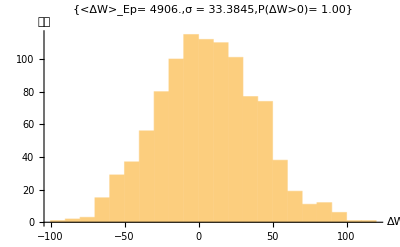

```mathematica
Histogram[Wall⟦1,All,1⟧-3000,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[Wall⟦1,All,1⟧-3000]]],"σ = "<>ToString[N[StandardDeviation[Wall⟦1,All,1⟧-3000]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[Wall⟦1,All,1⟧-3000]],3]]}]
```

```mathematica
Ep=1000;
```

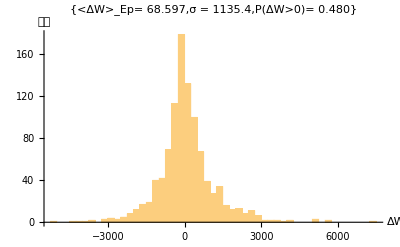

```mathematica
Histogram[Wall⟦All,2⟧-100,{250},AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[Wall⟦All,2⟧-100]]],"σ = "<>ToString[N[StandardDeviation[Wall⟦All,2⟧-100]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[Wall⟦All,2⟧-100]],3]]}]
```

```mathematica
Ep=3000;
```

```mathematica
WM=N[Mean[Wall⟦All,3⟧]-3000]
```

86.3365

```mathematica
WS=StandardDeviation[N[Wall⟦All,3⟧]]
```

174.064

```mathematica
Ep=3000;
```

```mathematica
PW=N[1/Ep Total[UnitStep[N[Wall⟦All,3⟧-3000]]],3]
```

0.627

```mathematica
N[Wall⟦All,3⟧];
```

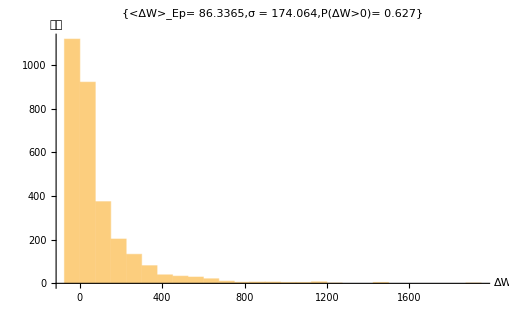

```mathematica
Histogram[Wall⟦All,3⟧-3000,{75},AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[WM],"σ = "<>ToString[N[WS]],"P(ΔW>0)= "<>ToString[PW]}]
```

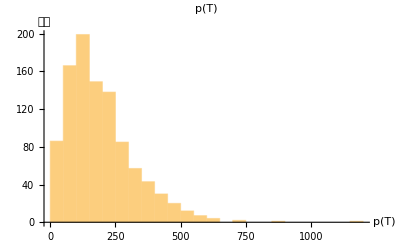

```mathematica
Histogram[Wall⟦1,All,4⟧,AxesLabel->{"p(T)",次數},PlotLabel-> "p(T)"]
```